# A mathematical model for universal semantics (Text mining in Hungarian)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a Hungarian translation of Jane Austen’s Pride and Prejudice is freely available from http://mek.oszk.hu/00300/00317/

After manual cleansing, we save the text as Büszkeség és balítélet.txt,  which begins with

1. FEJEZET
Általánosan elismert igazság, hogy a legényembernek, ha vagyonos, okvetlenül kell feleség.
Ez az igazság oly mélyen bevésődött a vidéki családok lelkébe, hogy ha ilyen ember csöppen a
szoms

and ends with

Darcy éppúgy szívből szerette őket, mint
Elizabeth; mindketten meleg hálát éreztek irántuk, akik Derbyshire-be hozták Elizát, s ezzel lehetővé
tették egybekelésüket.
Büszkeség és balítélet - 199/199 -

The current Mathematica Notebook demonstrates the analysis of Pride and Prejudice. For the analysis of other texts in our current work, one needs to download text corpora and modify the codes slightly.

### Jane Eyre

The full text  for a Hungarian translation of Charlotte Brontë’s Jane Eyre is freely available from http://mek.oszk.hu/05600/05680/

After manual cleansing, the text begins with

ELSŐ FEJEZET
Aznap szó sem lehetett a délutáni sétáról. Reggel még járkáltunk egy óra hosszat a kert kopár bokrai között, de ebéd után (ha nem volt vendég, Mrs. Reed korán ebédelt) a hideg téli szél o

and ends with

remtőjének. Utolsó levelében ezt írta:
„Az én Uram már figyelmeztetett engem, és mindennap érthetőbben adja tudtomra, hogy jön, és én óráról órára boldogabban felelem: - Úgy legyen, jöjj, Uram Jézus!”

### Origin of Species

The full text  for a Hungarian translation of Charles Darwin’s Origin of Species is freely available from http://mek.oszk.hu/05000/05011/

After manual cleansing, the text begins with

I. Fejezet -
A háziasítás során végbemenő változások 
Ha régebbi kultúrnövényeink vagy tenyészállataink egy-egy megadott fajtájának az egyedeit egymással összehasonlítjuk, az első, ami a szemünkbe tűn

and ends with

bolygónk a gravitáció megmásíthatatlan törvényét követve keringett körbe-körbe, ebből az egyszerű kezdetből kiindulva végtelenül sokféle, csodálatos és gyönyörű forma bontakozott ki – és teszi ma is.

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## Hungarian

## Hungarian stop words

We start from the following Hungarian stop word list (prepared by Anna Tordai) available at

http://snowball.tartarus.org/algorithms/hungarian/stop.txt

```mathematica
HungarianStopWords0=Complement[{"a","ahogy","ahol","aki","akik","akkor","alatt","által","általában","amely","amelyek","amelyekben","amelyeket","amelyet","amelynek","ami","amit","amolyan","amíg","amikor","át","abban","ahhoz","annak","arra","arról","az","azok","azon","azt","azzal","azért","aztán","azután","azonban","bár","be","belül","benne","cikk","cikkek","cikkeket","csak","de","e","eddig","egész","egy","egyes","egyetlen","egyéb","egyik","egyre","ekkor","el","elég","ellen","elő","először","előtt","első","én","éppen","ebben","ehhez","emilyen","ennek","erre","ez","ezt","ezek","ezen","ezzel","ezért","és","fel","felé","hanem","hiszen","hogy","hogyan","igen","így","illetve","ill.","ill","ilyen","ilyenkor","ison","ismét","itt","kell","kellett","keresztül","keressünk","ki","kívül","között","közül","legalább","lehet","lehetett","legyen","lenne","lenni","lesz","lett","maga","magát","majd","majd","már","más","másik","meg","még","mellett","mert","mely","melyek","mi","mit","míg","miért","milyen","mikor","minden","mindent","mindenki","mindig","mint","mintha","mivel","most","nagy","nagyobb","nagyon","ne","néha","nekem","neki","nem","néhány","nélkül","nincs","olyan","ott","össze","ő","ők","őket","pedig","persze","rá","s","saját","sem","semmi","sok","sokat","sokkal","számára","szemben","szerint","szinte","talán","tehát","teljes","tovább","továbbá","több","úgy","ugyanis","új","újabb","újra","után","utána","utolsó","vagy","vagyis","valaki","valami","valamint","való","vagyok","van","vannak","volt","voltam","voltak","voltunk","vissza","vele","viszont","volna"},{"nagy","nagyobb","új","újabb","jó","jól","jobban"}]
```

{a,abban,ahhoz,ahogy,ahol,aki,akik,akkor,alatt,által,általában,amely,amelyek,amelyekben,amelyeket,amelyet,amelynek,ami,amíg,amikor,amit,amolyan,annak,arra,arról,át,az,azért,azok,azon,azonban,azt,aztán,azután,azzal,bár,be,belül,benne,cikk,cikkek,cikkeket,csak,de,e,ebben,eddig,egész,egy,egyéb,egyes,egyetlen,egyik,egyre,ehhez,ekkor,el,elég,ellen,elő,először,előtt,első,emilyen,én,ennek,éppen,erre,és,ez,ezek,ezen,ezért,ezt,ezzel,fel,felé,hanem,hiszen,hogy,hogyan,igen,így,ill,ill.,illetve,ilyen,ilyenkor,ismét,ison,itt,kell,kellett,keressünk,keresztül,ki,kívül,között,közül,legalább,legyen,lehet,lehetett,lenne,lenni,lesz,lett,maga,magát,majd,már,más,másik,meg,még,mellett,mely,melyek,mert,mi,miért,míg,mikor,milyen,minden,mindenki,mindent,mindig,mint,mintha,mit,mivel,most,nagyon,ne,néha,néhány,nekem,neki,nélkül,nem,nincs,ő,ők,őket,olyan,össze,ott,pedig,persze,rá,s,saját,sem,semmi,sok,sokat,sokkal,számára,szemben,szerint,szinte,talán,tehát,teljes,több,tovább,továbbá,úgy,ugyanis,újra,után,utána,utolsó,vagy,vagyis,vagyok,valaki,valami,valamint,való,van,vannak,vele,vissza,viszont,volna,volt,voltak,voltam,voltunk}

We incorporate the complete conjugation of the Hungarian verb for “to be”, which is highly irregular:

```mathematica
beHungarian={"leendő","légy","legyek","legyél","legyen","legyenek","legyetek","legyünk","lehet","lenne","lenned","lennék","lennél","lennem","lennének","lennénk","lennetek","lennétek","lenni","lennie","lenniük","lennünk","lesz","leszek","leszel","lesznek","lesztek","leszünk","lett","lettek","lettél","lettem","lettetek","lettünk","lévén","levő","lévő","vagy","vagyok","vagytok","vagyunk","van","vannak","volna","volnál","volnának","volnánk","volnátok","volnék","volt","voltak","voltál","voltam","voltatok","voltunk"};
```

We also take all the Hungarian pronouns, their declensions, and their amalgamations with postpositions, from https://en.wikipedia.org/wiki/Hungarian_noun_phrase

```mathematica
pronounsHungarian={"én","engem","mi","minket","bennünket","te","maga","ön","téged","magát","önt","ti","maguk","önök","titeket","benneteket","magukat","önöket","ő","őt","ők","őket","nálam","nálad","nála","nálunk","nálatok","náluk","rólam","rólad","róla","rólunk","rólatok","róluk","rám","rád","rá","ránk","rátok","rájuk","hozzám","hozzád","hozzá","hozzánk","hozzátok","hozzájuk","rajtam","rajtad","rajta","rajtunk","rajtatok","rajtuk","velem","veled","vele","velünk","veletek","velük","tőlem","tőled","tőle","tőlünk","tőletek","tőlük","értem","érted","érte","értünk","értetek","értük","nekem","neked","neki","nekünk","nektek","nekik","bennem","benned","benne","bennünk","bennetek","bennük","belőlem","belőled","belőle","belőlünk","belőletek","belőlük","belém","beléd","belé","belénk","belétek","beléjük"}∪{"belőlem","énbelőlem","belőlünk","mibelőlünk","belőled","tebelőled","belőletek","tibelőletek","belőle","őbelőle","belőlük","őbelőlük"}∪{"alól","alólam","alólad","alóla","alólunk","alólatok","alóluk","fölül","fölülem","fölüled","fölüle","fölülünk","fölületek","fölülük","mellől","mellőlem","mellőled","mellőle","mellőlünk","mellőletek","mellőlük","elől","előlem","előled","előle","előlünk","előletek","előlük","mögül","mögülem","mögüled","mögüle","mögülünk","mögületek","mögülük","közül","közülem","közüled","közüle","közülünk","közületek","közülük","felől","felőlem","felőled","felőle","felőlünk","felőletek","felőlük","alatt","alattam","alattad","alatta","alattunk","alattatok","alattuk","fölött","fölöttem","fölötted","fölötte","fölöttünk","fölöttetek","fölöttük","mellett","mellettem","melletted","mellette","mellettünk","mellettetek","mellettük","előtt","előttem","előtted","előtte","előttünk","előttetek","előttük","mögött","mögöttem","mögötted","mögötte","mögöttünk","mögöttetek","mögöttük","között","közt","közöttem","köztem","közötted","közted","közötte","közte","közöttünk","köztünk","közöttetek","köztetek","közöttük","köztük","körül","körülöttem","körülötted","körülötte","körülöttünk","körülöttetek","körülöttük","alá","alám","alád","alá","alánk","alátok","alájuk","fölé","fölém","föléd","fölé","fölénk","fölétek","föléjük","mellé","mellém","melléd","mellé","mellénk","mellétek","melléjük","elé","elém","eléd","elé","elénk","elétek","eléjük","mögé","mögém","mögéd","mögé","mögénk","mögétek","mögéjük","közé","közém","közéd","közé","közénk","közétek","közéjük","köré","körém","köréd","köré","körénk","körétek","köréjük","felé","felém","feléd","felé","felénk","felétek","feléjük","után","utánam","utánad","utána","utánunk","utánatok","utánuk","helyett","helyettem","helyetted","helyette","helyettünk","helyettetek","helyettük","nélkül","nélkülem","nélküled","nélküle","nélkülünk","nélkületek","nélkülük","által","általam","általad","általa","általunk","általatok","általuk","ellen","ellenem","ellened","ellene","ellenünk","ellenetek","ellenük","miatt","miattam","miattad","miatta","miattunk","miattatok","miattuk","végett","szerint","szerintem","szerinted","szerinte","szerintünk","szerintetek","szerintük","iránt","irántam","irántad","iránta","irántunk","irántatok","irántuk"}∪{"részemre","részedre","részére","részünkre","részetekre","részükre","számomra","számodra","számára","számunkra","számotokra","számukra","révemen","réveden","révén","révünkön","réveteken","révükön","segítségemmel","segítségeddel","segítségével","segítségünkkel","segítségetekkel","segítségükkel","esetemben","esetedben","esetében","esetünkben","esetetekben","esetükben","részemről","részedről","részéről","részünkről","részetekről","részükről"}∪{"egymás","egymásba","egymásban","egymásból","egymásért","egymáshoz","egymásig","egymásként","egymásnak","egymásnál","egymáson","egymásra","egymásról","egymássá","egymással","egymást","egymástól"}∪{"kegyed","kegyedet","kegyednek","kegyeddel","kegyedért","kegyeddé","kegyedig","kegyedként","kegyedben","kegyeden","kegyednél","kegyedbe","kegyedre","kegyedhez","kegyedből","kegyedről","kegyedtől"};
```

```mathematica
thisHungarian=""|"ugyan"|"mind"~~Alternatives@@{"ebbe","ebben","ebből","eddig","ehhez","ekként","ennek","ennél","erre","erről","ettől","ez","ezek","ezekbe","ezekben","ezekből","ezeken","ezekért","ezeket","ezekhez","ezekig","ezekké","ezekkel","ezekként","ezeknek","ezeknél","ezekre","ezekről","ezektől","ezen","ezért","ezt","ezzé","ezzel"};
```

```mathematica
whichthatHungarian=""|"a"|"bár"|"né"|"vala"~~"mely"~~""|"be"|"ben"|"ből"|"ek"|"ekbe"|"ekben"|"ekből"|"eken"|"ekért"|"eket"|"ekhez"|"ekig"|"ekké"|"ekkel"|"ekként"|"eknek"|"eknél"|"ekre"|"ekről"|"ektől"|"en"|"ért"|"et"|"hez"|"ig"|"ként"|"nek"|"nél"|"re"|"ről"|"től"
```

|a|bár|né|vala~~mely~~|be|ben|ből|ek|ekbe|ekben|ekből|eken|ekért|eket|ekhez|ekig|ekké|ekkel|ekként|eknek|eknél|ekre|ekről|ektől|en|ért|et|hez|ig|ként|nek|nél|re|ről|től

```mathematica
whatsoeverHungarian="af"|"ef"|"mi"|"ki"|"semmi"~~"fél"~~"e"|"é"~~""|"k"~~""|"be"|"ben"|"ből"|"en"|"ént"|"ért"|"et"|"hez"|"ig"|"ké"|"kel"|"ként"|"n"|"nek"|"nél"|"re"|"ről"|"t"|"től"|"vé"|"vel";
```

```mathematica
thatHungarian=""|"ugyan"|"mind"~~Alternatives@@{"abba","abban","abból","addig","ahhoz","akként","annak","annál","arra","arról","attól","az","azért","azok","azokat","azokba","azokban","azokból","azokért","azokhoz","azokig","azokká","azokkal","azokként","azoknak","azoknál","azokon","azokra","azokról","azoktól","azon","azt","azzá","azzal"};
```

```mathematica
aHungarian={"eggyé","eggyel","egy","egybe","egyben","egyből","egye","egyed","egyem","egyen","egyért","egyet","egyetek","egyhez","egyig","egyként","egynek","egynél","egyre","egyről","egytől","együk","együnk"};
```

```mathematica
postpositionsHungarian={"át","keresztül","túl","óta","hosszat","múlva","kezdve","közben","során","folyamán","körül","tájt","tájban","táján","gyanánt","végett","esetén","folytán","képest","nézve"}∪{"valami","valamit","valaminek","ellenére","folyamán","jóvoltából","kedvéért","következtében","mentén","részére","révén","számára","útján","valamin","alul","át","belül","felül","fölül","innen","keresztül","kezdve","kívül","túl","valamire","nézve","valamihez","hasonlóan","képest","valaminél","fogva","valamitől","kezdve","valamivel","együtt","szemben"};
```

```mathematica
somethingHungarian={"valami","valamik","valamit","valamiket","valaminek","valamiknek","valamivel","valamikkel","valamiért","valamikért","valamivé","valamikké","valamiig","valamikig","valamiként","valamikként","valamiben","valamikben","valamin","valamiken","valaminél","valamiknél","valamibe","valamikbe","valamire","valamikre","valamihez","valamikhez","valamiből","valamikből","valamiről","valamikről","valamitől","valamiktől","valami","valamim","valamijeim","valamid","valamijeid","valamije","valamijei","valamink","valamijeink","valamitek","valamijeitek","valamijük","valamijeik"};
```

```mathematica
someoneHungarian={"valaki","valakik","valakit","valakiket","valakinek","valakiknek","valakivel","valakikkel","valakiért","valakikért","valakivé","valakikké","valakiig","valakikig","valakiként","valakikként","valakiben","valakikben","valakin","valakiken","valakinél","valakiknél","valakibe","valakikbe","valakire","valakikre","valakihez","valakikhez","valakiből","valakikből","valakiről","valakikről","valakitől","valakiktől","valaki","valakim","valakijeim","valakid","valakijeid","valakije","valakijei","valakink","valakijeink","valakitek","valakijeitek","valakijük","valakijeik"};
```

```mathematica
thismuchHungarian={"ennyi","ennyik","ennyit","ennyiket","ennyinek","ennyiknek","ennyivel","ennyikkel","ennyiért","ennyikért","ennyivé","ennyikké","ennyiig","ennyikig","ennyiként","ennyikként","ennyiben","ennyikben","ennyin","ennyiken","ennyinél","ennyiknél","ennyibe","ennyikbe","ennyire","ennyikre","ennyihez","ennyikhez","ennyiből","ennyikből","ennyiről","ennyikről","ennyitől","ennyiktől","ennyi","ennyim","ennyijeim","ennyid","ennyijeid","ennyije","ennyijei","ennyink","ennyijeink","ennyitek","ennyijeitek","ennyijük","ennyijeik"};
```

```mathematica
willHungarian={"fogok","fogsz","fog","fogunk","fogtok","fognak","fogom","fogod","fogja","fogjuk","fogjátok","fogják"};
```

```mathematica
thatmuchHungarian={"annyi","annyit","annyinak","annyival","annyiért","annyivá","annyiig","annyiként","annyiban","annyin","annyinál","annyiba","annyira","annyihoz","annyiból","annyiról","annyitól","annyiszor"};
```

```mathematica
HungarianStopWords=HungarianStopWords0∪beHungarian∪aHungarian∪pronounsHungarian∪thatmuchHungarian∪willHungarian∪postpositionsHungarian∪{"is","ha","együtt","ugye","e","annyiszor","hol","se","le","fel","föl","benn","bent","kinn","kint","fent","fenn","oly","olyan","olyat","olykor","ily","ilyen","miatt","helyett","felett","fele","megint","kijjebb","beljebb","följebb","lejjebb"}∪{"ön","önbe","önben","önből","önért","önhöz","önig","önként","önné","önnek","önnel","önnél","önök","önökbe","önökben","önökből","önökért","önöket","önökhöz","önökig","önökké","önökkel","önökként","önöknek","önöknél","önökön","önökre","önökről","önöktől","önön","önre","önről","önt","öntől"}∪{"légy","legyek","legyél","legyen","legyenek","legyetek","legyünk","lehet","lenne","lenned","lennék","lennél","lennem","lennének","lennénk","lennetek","lennétek","lenni","lennie","lenniük","lennünk","lesz","leszek","leszel","lesznek","lesztek","leszünk","lett","lettek","lettél","lettem","lettetek","lettünk","léve","levő"}∪{"merthogy","noha","akár","tehát","így","azaz","vagyis","nemcsak","alig","aligha"}∪{"bárcsak","esetleg","alighanem","dehogy","bizony","hogyne"}∪{"mind","mindbe","mindben","mindből","minddé","minddel","minden","mindért","mindet","mindhez","mindig","mindként","mindnek","mindnél","mindre","mindről","mindtől"}∪{"alighogy","máris","úgyis","hogyha","mielőtt","miután","ellenben","mégis"}∪{"lenn","lent","ahogyan","valahol","valamikor","valahogyan","bárhol","bármikor","bárhogyan","azzonal","rögtön","ide","oda"}∪{"hány"}∪{"sincs","sincsen"}∪{"ugyan"}∪{"soha","sohasem"}∪{"néhánnyá","néhánnyal","néhány","néhányat","néhányba","néhányban","néhányból","néhányért","néhányhoz","néhányig","néhányként","néhánynak","néhánynál","néhányon","néhányra","néhányról","néhánytól","néhol","némellyé","némellyel","némely","némelybe","némelyben","némelyből","némelyek","némelyekbe","némelyekben","némelyekből","némelyeken","némelyekért","némelyeket","némelyekhez","némelyekig","némelyekké","némelyekkel","némelyekként","némelyeknek","némelyeknél","némelyekre","némelyekről","némelyektől","némelyen","némelyért","némelyet","némelyhez","némelyig","némelyik","némelyikbe","némelyikben","némelyikből","némelyiken","némelyikért","némelyiket","némelyikhez","némelyikig","némelyikké","némelyikkel","némelyikként","némelyiknek","némelyiknél","némelyikre","némelyikről","némelyiktől","némelyként","némelynek","némelynél","némelyre","némelyről","némelytől","némi","némiképp","némiképpen","némileg"}∪{"sokféle","sokféleképp","sokféleképpen"}∪{"egyik","egyikbe","egyikben","egyikből","egyike","egyiked","egyikek","egyikekbe","egyikekben","egyikekből","egyikeken","egyikekért","egyikeket","egyikekhez","egyikekig","egyikekké","egyikekkel","egyikekként","egyikeknek","egyikeknél","egyikekre","egyikekről","egyikektől","egyikem","egyiken","egyikért","egyiket","egyiketek","egyikhez","egyikig","egyikké","egyikkel","egyikként","egyiknek","egyiknél","egyikre","egyikről","egyiktől","egyikük","egyikünk"}∪{"mindegyik","mindegyikbe","mindegyikben","mindegyikből","mindegyike","mindegyiked","mindegyikek","mindegyikekbe","mindegyikekben","mindegyikekből","mindegyikeken","mindegyikekért","mindegyikeket","mindegyikekhez","mindegyikekig","mindegyikekké","mindegyikekkel","mindegyikekként","mindegyikeknek","mindegyikeknél","mindegyikekre","mindegyikekről","mindegyikektől","mindegyikem","mindegyiken","mindegyikért","mindegyiket","mindegyiketek","mindegyikhez","mindegyikig","mindegyikké","mindegyikkel","mindegyikként","mindegyiknek","mindegyiknél","mindegyikre","mindegyikről","mindegyiktől","mindegyikük","mindegyikünk"}∪{"hát","dehát","hátha","nahát","tehát"}∪{"mihelyt","amint","újból","valaha","valahányszor","valamiképpen","valamerre"}∪{"más","mása","másai","másaid","másaik","másaim","másaink","másaitok","másba","másban","másból","másért","máshoz","másig","másként","másnak","másnál","másod","mások","másokat","másokba","másokban","másokból","másokért","másokhoz","másokig","másokká","másokkal","másokként","másoknak","másoknál","másokon","másokra","másokról","másoktól","másom","máson","másotok","másra","másról","mássá","mással","mást","mástól","másuk","másunk","máshonnan"}∪{"tedd","teendő","tegye","tegyed","tegyek","tegyék","tegyél","tegyelek","tegyem","tegyen","tegyenek","tegyetek","tegyétek","tegyük","tegyünk","tehet","tenne","tenné","tenned","tennéd","tennék","tennél","tennélek","tennem","tenném","tennének","tennénk","tennetek","tennétek","tenni","tennie","tenniük","tennünk","tesszük","tesz","teszed","teszek","teszel","teszem","teszi","teszik","teszitek","teszlek","tesznek","tesztek","teszünk","tett","tette","tetted","tettek","tették","tettél","tettelek","tettem","tettetek","tettétek","tettük","tettünk","tevő"}∪{"fenti","fentibe","fentiben","fentiből","fentiek","fentiekbe","fentiekben","fentiekből","fentieken","fentiekért","fentieket","fentiekhez","fentiekig","fentiekké","fentiekkel","fentiekként","fentieknek","fentieknél","fentiekre","fentiekről","fentiektől","fentiért","fentihez","fentiig","fentiként","fentin","fentinek","fentinél","fentire","fentiről","fentit","fentitől","fentivé","fentivel"}∪{"csinál","csinálandó","csináld","csinálhat","csinálj","csinálja","csináljad","csináljak","csinálják","csináljál","csináljalak","csináljam","csináljanak","csináljatok","csináljátok","csináljon","csináljuk","csináljunk","csinállak","csinálna","csinálná","csinálnád","csinálnak","csinálnák","csinálnál","csinálnálak","csinálnám","csinálnának","csinálnánk","csinálnátok","csinálnék","csinálni","csinálnia","csinálniuk","csinálnod","csinálnom","csinálnotok","csinálnunk","csináló","csinálod","csinálok","csinálom","csinálsz","csinált","csinálta","csináltad","csináltak","csinálták","csináltál","csináltalak","csináltam","csináltatok","csináltátok","csináltok","csináltuk","csináltunk","csinálunk","csinálva"}∪{"hadd"}∪{"honnan","ahonnan","akárhonnan","bárhonnan","máshonnan","mindenhonnan","sehonnan","valahonnan"}∪{"honnét","ahonnét","akárhonnét","bárhonnét","máshonnét","mindenhonnét","sehonnét","valahonnét"}∪{"hol","ahol","akárhol","bárhol","holott","máshol","mindenhol","néhol","sehol","valahol"}∪{"hova","ahova","akárhova","bárhova","máshova","mindenhova","sehova","valahova"}∪{"miközben","közben","közbeni","aközben","eközben","időközben"}∪{"egyébként","különben","másfelől","majdnem","majd","csaknem","szinte","majdhogynem","micsoda"}∪{"összes","összesen","sőt","nincsen","nincsenek","sincsenek","kivéve"};
```

```mathematica
posspronHungarian=("enyém"|"mienk"|"miénk"|"tied"|"tiéd"|"tietek"|"tiétek"|"magáé"|"maguké"|"öné"|"önöké"|"övé"|"övék"|"enyéim"|"mieink"|"tieid"|"tieitek"|"magáéi"|"magukéi"|"önéi"|"önökéi"|"övéi"|"övéik")~~(""|"ek"|"et"|"eket"|"nek"|"eknek"|"mel"|"del"|"kel"|"vel"|"ekkel"|"ért"|"ekért"|"mé"|"dé"|"ké"|"vé"|"ekké"|"ig"|"ekig"|"ként"|"ekként"|"ben"|"ekben"|"en"|"eken"|"nél"|"eknél"|"be"|"ekbe"|"re"|"ekre"|"hez"|"ekhez"|"ből"|"ekből"|"ről"|"ekről"|"től"|"ektől")
```

enyém|mienk|miénk|tied|tiéd|tietek|tiétek|magáé|maguké|öné|önöké|övé|övék|enyéim|mieink|tieid|tieitek|magáéi|magukéi|önéi|önökéi|övéi|övéik~~|ek|et|eket|nek|eknek|mel|del|kel|vel|ekkel|ért|ekért|mé|dé|ké|vé|ekké|ig|ekig|ként|ekként|ben|ekben|en|eken|nél|eknél|be|ekbe|re|ekre|hez|ekhez|ből|ekből|ről|ekről|től|ektől

```mathematica
magaHungarian=""|"jó"|"ön"~~"mag"~~"a"|"á"|("u"~~""|"n"~~"k")~~""|"d"|"m"|"tok"~~""|"at"|"ba"|"ban"|"ból"|"dá"|"dal"|"ért"|"hoz"|"ig"|"ká"|"kal"|"ként"|"má"|"mal"|"n"|"nak"|"nál"|"on"|"ra"|"ról"|"t"|"tól"|"vá"|"val";
```

```mathematica
oneHungarian=(""|"a"|"vala"|"sen"|"sem"|"akár"|"bár"|"minden")~~"k"|"m"~~"i"~~(""|"é"|"m"|"jeim"|"d"|"jeid"|"je"|"jei"|"nk"|"jeink"|"tek"|"jeitek"|"jük"|"jeik")~~""|"e"~~(""|"k"|"t"|"ket"|"nek"|"knek"|"mel"|"del"|"kel"|"vel"|"kkel"|"ért"|"kért"|"mé"|"dé"|"ké"|"vé"|"kké"|"ig"|"kig"|"ként"|"kként"|"ben"|"kben"|"n"|"ken"|"nél"|"knél"|"be"|"kbe"|"re"|"kre"|"hez"|"khez"|"ből"|"kből"|"ről"|"kről"|"től"|"ktől")
```

|a|vala|sen|sem|akár|bár|minden~~k|m~~i~~|é|m|jeim|d|jeid|je|jei|nk|jeink|tek|jeitek|jük|jeik~~|e~~|k|t|ket|nek|knek|mel|del|kel|vel|kkel|ért|kért|mé|dé|ké|vé|kké|ig|kig|ként|kként|ben|kben|n|ken|nél|knél|be|kbe|re|kre|hez|khez|ből|kből|ről|kről|től|ktől

```mathematica
thatkindHungarian=""|"épp"|"ugyan"~~"olyan"~~""|"ja"|"jai"|"jaid"|"jaik"|"jaim"|"jaink"|"jaitok"|"juk"|"od"|"om"|"otok"|"unk"~~""|"ba"|"ban"|"ból"|"ért"|"hoz"|"ig"|"ként"|"má"|"dá"|"ká"|"ná"|"nak"|"mal"|"dal"|"kal"|"nal"|"nál"|"ok"|"okat"|"okba"|"okban"|"okból"|"okért"|"okhoz"|"okig"|"okká"|"okkal"|"okként"|"oknak"|"oknál"|"okon"|"okra"|"okról"|"októl"|"on"|"ra"|"ról"|"t"|"tól"
```

|épp|ugyan~~olyan~~|ja|jai|jaid|jaik|jaim|jaink|jaitok|juk|od|om|otok|unk~~|ba|ban|ból|ért|hoz|ig|ként|má|dá|ká|ná|nak|mal|dal|kal|nal|nál|ok|okat|okba|okban|okból|okért|okhoz|okig|okká|okkal|okként|oknak|oknál|okon|okra|okról|októl|on|ra|ról|t|tól

```mathematica
muchHungarian=(""|"m"|"akárm"|"am"|"bárm"|"sem"|"valam"|"né"|"ugyan")~~"annyi"|"ennyi"|"ilyen"|"elyik"~~""|"e"~~""|"m"|"jeim"|"d"|"jeid"|"je"|"jei"|"nk"|"jeink"|"tek"|"jeitek"|"jük"|"jeik"~~""|"e"~~""|"k"|"t"|"ket"|"nek"|"knek"|"mel"|"del"|"kel"|"vel"|"kkel"|"ért"|"kért"|"mé"|"dé"|"ké"|"vé"|"kké"|"ig"|"kig"|"ként"|"kként"|"ben"|"kben"|"n"|"ken"|"nél"|"knél"|"be"|"kbe"|"re"|"kre"|"hez"|"khez"|"ből"|"kből"|"ről"|"kről"|"től"|"ktől"
```

|m|akárm|am|bárm|sem|valam|né|ugyan~~annyi|ennyi|ilyen|elyik~~|e~~|m|jeim|d|jeid|je|jei|nk|jeink|tek|jeitek|jük|jeik~~|e~~|k|t|ket|nek|knek|mel|del|kel|vel|kkel|ért|kért|mé|dé|ké|vé|kké|ig|kig|ként|kként|ben|kben|n|ken|nél|knél|be|kbe|re|kre|hez|khez|ből|kből|ről|kről|től|ktől

```mathematica
manyHungarian="sok"|"akárhány"|"valahány"|"néhány"|"ahány"~~""|"ak"|"at"|"akat"|"nak"|"aknak"|"kal"|"akkal"|"ért"|"akért"|"ká"|"akká"|"ig"|"akig"|"ként"|"akként"|"ban"|"akban"|"on"|"akon"|"nál"|"aknál"|"ba"|"akba"|"ra"|"akra"|"hoz"|"akhoz"|"ból"|"akból"|"ról"|"akról"|"tól"|"aktól"
```

sok|akárhány|valahány|néhány|ahány~~|ak|at|akat|nak|aknak|kal|akkal|ért|akért|ká|akká|ig|akig|ként|akként|ban|akban|on|akon|nál|aknál|ba|akba|ra|akra|hoz|akhoz|ból|akból|ról|akról|tól|aktól

```mathematica
fewmoreHungarian=("kevés"|"kevesebb"|"legkevesebb"|"több"|"legtöbb")~~(""|"em"|"jeim"|"ed"|"jeid"|"je"|"jei"|"ünk"|"jeink"|"etek"|"jeitek"|"jük"|"jeik"~~""|"m"|"d"|"k"|"v")~~(""|"ek"|"et"|"eket"|"nek"|"eknek"|"el"|"ekkel"|"ért"|"ekért"|"é"|"ekké"|"ig"|"ekig"|"ként"|"ekként"|"en"|"ekben"|"en"|"eken"|"nél"|"eknél"|"e"|"ekbe"|"re"|"ekre"|"hez"|"ekhez"|"ől"|"ekből"|"ről"|"ekről"|"től"|"ektől")
```

kevés|kevesebb|legkevesebb|több|legtöbb~~|em|jeim|ed|jeid|je|jei|ünk|jeink|etek|jeitek|jük|jeik~~|m|d|k|v~~|ek|et|eket|nek|eknek|el|ekkel|ért|ekért|é|ekké|ig|ekig|ként|ekként|en|ekben|en|eken|nél|eknél|e|ekbe|re|ekre|hez|ekhez|ől|ekből|ről|ekről|től|ektől

```mathematica
sizeHungarian=(""|"akár"|"bár"|"se")~~("ak"|"ek"|"mek"|"jó")~~"kor"~~("a"|"ába"|"ában"|"ából"|"áért"|"ához"|"áig"|"ák"|"ákat"|"ákba"|"ákban"|"ákból"|"aként"|"ákért"|"ákhoz"|"ákig"|"ákká"|"ákkal"|"ákként"|"áknak"|"áknál"|"ákon"|"ákra"|"ákról"|"áktól"|"án"|"ának"|"ánál"|"ára"|"áról"|"át"|"ától"|"ává"|"ával")
```

|akár|bár|se~~ak|ek|mek|jó~~kor~~a|ába|ában|ából|áért|ához|áig|ák|ákat|ákba|ákban|ákból|aként|ákért|ákhoz|ákig|ákká|ákkal|ákként|áknak|áknál|ákon|ákra|ákról|áktól|án|ának|ánál|ára|áról|át|ától|ává|ával

```mathematica
whichHungarian=""|"a"~~"h"~~"a"|"á"~~"nyadik"~~""|"ak"|"akat"|"akba"|"akban"|"akból"|"akért"|"akhoz"|"akig"|"akká"|"akkal"|"akként"|"aknak"|"aknál"|"akon"|"akra"|"akról"|"aktól"|"at"|"ba"|"ban"|"ból"|"ért"|"hoz"|"ig"|"ká"|"kal"|"ként"|"nak"|"nál"|"ok"|"okat"|"okba"|"okban"|"okból"|"okért"|"okhoz"|"okig"|"okká"|"okkal"|"okként"|"oknak"|"oknál"|"okon"|"okra"|"okról"|"októl"|"on"|"ot"|"ra"|"ról"|"tól"
```

|a~~h~~a|á~~nyadik~~|ak|akat|akba|akban|akból|akért|akhoz|akig|akká|akkal|akként|aknak|aknál|akon|akra|akról|aktól|at|ba|ban|ból|ért|hoz|ig|ká|kal|ként|nak|nál|ok|okat|okba|okban|okból|okért|okhoz|okig|okká|okkal|okként|oknak|oknál|okon|okra|okról|októl|on|ot|ra|ról|tól

```mathematica
whereHungarian=""|"a"|"akár"|"bár"|"más"|"né"|"ne"|"mint"|"minden"|"se"|"vala"~~"ho"~~"gy"|"l"|"va"|"vá";
```

## Hungarian sample words

The following samples of regular nouns (declined in all cases, in singular and plural) are extracted from Appendix 2 of Rounds’ grammar book.

```mathematica
houseHungarian={"ház","házak","házakat","házakba","házakban","házakból","házakért","házakhoz","házakig","házakká","házakkal","házakként","házaknak","házaknál","házakon","házakra","házakról","házaktól","házanként","házastul","házat","házba","házban","házból","házért","házhoz","házig","házként","háznak","háznál","házon","házra","házról","háztól","házzá","házzal"};
```

```mathematica
bookHungarian={"könyv","könyvbe","könyvben","könyvből","könyvek","könyvekbe","könyvekben","könyvekből","könyveken","könyvekért","könyveket","könyvekhez","könyvekig","könyvekké","könyvekkel","könyvekként","könyveknek","könyveknél","könyvekre","könyvekről","könyvektől","könyvenként","könyvért","könyvestül","könyvet","könyvhöz","könyvig","könyvként","könyvnek","könyvnél","könyvön","könyvre","könyvről","könyvtől","könyvvé","könyvvel"};
```

```mathematica
glassHungarian={"pohár","poharak","poharakat","poharakba","poharakban","poharakból","poharakért","poharakhoz","poharakig","poharakká","poharakkal","poharakként","poharaknak","poharaknál","poharakon","poharakra","poharakról","poharaktól","poharanként","poharastul","poharat","pohárba","pohárban","pohárból","pohárért","pohárhoz","pohárig","pohárként","pohárnak","pohárnál","poháron","pohárra","pohárrá","pohárral","pohárról","pohártól"};
```

```mathematica
handHungarian={"kéz","kézbe","kézben","kézből","kezek","kezekbe","kezekben","kezekből","kezeken","kezekért","kezeket","kezekhez","kezekig","kezekké","kezekkel","kezekként","kezeknek","kezeknél","kezekre","kezekről","kezektől","kézen","kezenként","kézért","kezestül","kezet","kézhez","kézig","kézként","kéznek","kéznél","kézre","kézről","kéztől","kézzé","kézzel"};
```

```mathematica
bagHungarian={"táska","táskába","táskában","táskából","táskáért","táskához","táskáig","táskák","táskákat","táskákba","táskákban","táskákból","táskaként","táskákért","táskákhoz","táskákig","táskákká","táskákkal","táskákként","táskáknak","táskáknál","táskákon","táskákra","táskákról","táskáktól","táskán","táskának","táskánál","táskánként","táskára","táskáról","táskástul","táskát","táskától","táskává","táskával"};
```

```mathematica
melonHungarian={"dinnye","dinnyébe","dinnyében","dinnyéből","dinnyéért","dinnyéhez","dinnyéig","dinnyék","dinnyékbe","dinnyékben","dinnyékből","dinnyéken","dinnyeként","dinnyékért","dinnyéket","dinnyékhez","dinnyékig","dinnyékké","dinnyékkel","dinnyékként","dinnyéknek","dinnyéknél","dinnyékre","dinnyékről","dinnyéktől","dinnyén","dinnyének","dinnyénél","dinnyénként","dinnyére","dinnyéről","dinnyéstül","dinnyét","dinnyétől","dinnyévé","dinnyével"};
```

```mathematica
girlHungarian={"lánnyá","lánnyal","lány","lányastul","lányba","lányban","lányból","lányért","lányhoz","lányig","lányként","lánynak","lánynál","lányok","lányokat","lányokba","lányokban","lányokból","lányokért","lányokhoz","lányokig","lányokká","lányokkal","lányokként","lányoknak","lányoknál","lányokon","lányokra","lányokról","lányoktól","lányon","lányonként","lányra","lányról","lányt","lánytól"};
```

```mathematica
chairHungarian={"szék","székbe","székben","székből","székek","székekbe","székekben","székekből","székeken","székekért","székeket","székekhez","székekig","székekké","székekkel","székekként","székeknek","székeknél","székekre","székekről","székektől","széken","székenként","székért","székestül","széket","székhez","székig","székké","székkel","székként","széknek","széknél","székre","székről","széktől"};
```

```mathematica
guardHungarian={"őr","őrbe","őrben","őrből","őrért","őrestül","őrhöz","őrig","őrként","őrnek","őrnél","őrök","őrökbe","őrökben","őrökből","őrökért","őröket","őrökhöz","őrökig","őrökké","őrökkel","őrökként","őröknek","őröknél","őrökön","őrökre","őrökről","őröktől","őrön","őrönként","őrre","őrré","őrrel","őrről","őrt","őrtől"};
```

```mathematica
bushHungarian={"bokor","bokorba","bokorban","bokorból","bokorért","bokorhoz","bokorig","bokorként","bokornak","bokornál","bokorra","bokorrá","bokorral","bokorról","bokortól","bokrok","bokrokat","bokrokba","bokrokban","bokrokból","bokrokért","bokrokhoz","bokrokig","bokrokká","bokrokkal","bokrokként","bokroknak","bokroknál","bokrokon","bokrokra","bokrokról","bokroktól","bokron","bokronként","bokrostul","bokrot"};
```

```mathematica
twinHungarian={"iker","ikerbe","ikerben","ikerből","ikerért","ikerhez","ikerig","ikerként","ikernek","ikernél","ikerre","ikerré","ikerrel","ikerről","ikertől","ikrek","ikrekbe","ikrekben","ikrekből","ikreken","ikrekért","ikreket","ikrekhez","ikrekig","ikrekké","ikrekkel","ikrekként","ikreknek","ikreknél","ikrekre","ikrekről","ikrektől","ikren","ikrenként","ikrestül","ikret"};
```

```mathematica
mirrorHungarian={"tükör","tükörbe","tükörben","tükörből","tükörért","tükörhöz","tükörig","tükörként","tükörnek","tükörnél","tükörre","tükörré","tükörrel","tükörről","tükörtől","tükrök","tükrökbe","tükrökben","tükrökből","tükrökért","tükröket","tükrökhöz","tükrökig","tükrökké","tükrökkel","tükrökként","tükröknek","tükröknél","tükrökön","tükrökre","tükrökről","tükröktől","tükrön","tükrönként","tükröstül","tükröt"};
```

```mathematica
lakeHungarian={"tavak","tavakat","tavakba","tavakban","tavakból","tavakért","tavakhoz","tavakig","tavakká","tavakkal","tavakként","tavaknak","tavaknál","tavakon","tavakra","tavakról","tavaktól","tavanként","tavastul","tavat","tavon","tó","tóba","tóban","tóból","tóért","tóhoz","tóig","tóként","tónak","tónál","tóra","tóról","tótól","tóvá","tóval"};
```

```mathematica
stoneHungarian={"kő","kőbe","kőben","kőből","kőért","kőhöz","kőig","kőként","kőnek","kőnél","kőre","kőről","kőtől","kővé","kövek","kövekbe","kövekben","kövekből","köveken","kövekért","köveket","kövekhez","kövekig","kövekké","kövekkel","kövekként","köveknek","köveknél","kövekre","kövekről","kövektől","kővel","kövenként","kövestül","követ","kövön"};
```

```mathematica
wordHungarian={"szavak","szavakat","szavakba","szavakban","szavakból","szavakért","szavakhoz","szavakig","szavakká","szavakkal","szavakként","szavaknak","szavaknál","szavakon","szavakra","szavakról","szavaktól","szavanként","szavastul","szavon","szó","szóba","szóban","szóból","szóért","szóhoz","szóig","szók","szóként","szónak","szónál","szóra","szóról","szót","szótól","szóvá","szóval"};
```

```mathematica
my♯houseHungarian={"házaim","házaimat","házaimba","házaimban","házaimból","házaimért","házaimhoz","házaimig","házaimmá","házaimmal","házaimnak","házaimnál","házaimon","házaimra","házaimról","házaimtól","házam","házamat","házamba","házamban","házamból","házamért","házamhoz","házamig","házamként","házammá","házammal","házamnak","házamnál","házamon","házamra","házamról","házamtól"}∪{"ház"};
```

```mathematica
your♯letterHungarian={"leveled","leveledbe","leveledben","leveledből","leveleddé","leveleddel","leveleden","leveledért","leveledet","leveledhez","leveledig","leveledként","levelednek","levelednél","leveledre","leveledről","leveledtől","leveleid","leveleidbe","leveleidben","leveleidből","leveleiddé","leveleiddel","leveleiden","leveleidért","leveleidet","leveleidhez","leveleidig","leveleidnek","leveleidnél","leveleidre","leveleidről","leveleidtől"}∪{"levél"};
```

```mathematica
his♯her♯horseHungarian={"lova","lovába","lovában","lovából","lováért","lovához","lovai","lovaiba","lovaiban","lovaiból","lovaiért","lováig","lovaihoz","lovaiig","lovaiként","lovain","lovainak","lovainál","lovaira","lovairól","lovait","lovaitól","lovaivá","lovaival","lovaként","lován","lovának","lovánál","lovára","lováról","lovát","lovától","lovává","lovával"};
```

```mathematica
our♯rewardHungarian={"jutalmaink","jutalmainkat","jutalmainkba","jutalmainkban","jutalmainkból","jutalmainkért","jutalmainkhoz","jutalmainkig","jutalmainkká","jutalmainkkal","jutalmainknak","jutalmainknál","jutalmainkon","jutalmainkra","jutalmainkról","jutalmainktól","jutalmunk","jutalmunkat","jutalmunkba","jutalmunkban","jutalmunkból","jutalmunkért","jutalmunkhoz","jutalmunkig","jutalmunkká","jutalmunkkal","jutalmunkként","jutalmunknak","jutalmunknál","jutalmunkon","jutalmunkra","jutalmunkról","jutalmunktól"}∪{"jutalom"};
```

```mathematica
your♯dreamHungarian={"álmaitok","álmaitokat","álmaitokba","álmaitokban","álmaitokból","álmaitokért","álmaitokhoz","álmaitokig","álmaitokká","álmaitokkal","álmaitoknak","álmaitoknál","álmaitokon","álmaitokra","álmaitokról","álmaitoktól","álmotok","álmotokat","álmotokba","álmotokban","álmotokból","álmotokért","álmotokhoz","álmotokig","álmotokká","álmotokkal","álmotokként","álmotoknak","álmotoknál","álmotokon","álmotokra","álmotokról","álmotoktól"}∪{"álom"};
```

```mathematica
their♯pictureHungarian={"képeik","képeikbe","képeikben","képeikből","képeiken","képeikért","képeiket","képeikhez","képeikig","képeikké","képeikkel","képeiknek","képeiknél","képeikre","képeikről","képeiktől","képük","képükbe","képükben","képükből","képükért","képüket","képükhöz","képükig","képükké","képükkel","képükként","képüknek","képüknél","képükön","képükre","képükről","képüktől"}∪{"kép"};
```

```mathematica
appleHungarian={"alma","almák","almát","almákat","almának","almáknak","almával","almákkal","almáért","almákért","almává","almákká","almáig","almákig","almaként","almákként","almában","almákban","almán","almákon","almánál","almáknál","almába","almákba","almára","almákra","almához","almákhoz","almából","almákból","almáról","almákról","almától","almáktól","alma","almám","almáim","almád","almáid","almája","almái","almánk","almáink","almátok","almáitok","almájuk","almáik"};
```

```mathematica
HungarianSampleRegularNouns=houseHungarian∪bookHungarian∪glassHungarian∪handHungarian∪bagHungarian∪melonHungarian∪girlHungarian∪chairHungarian∪guardHungarian∪bushHungarian∪twinHungarian∪mirrorHungarian∪lakeHungarian∪stoneHungarian∪wordHungarian∪my♯houseHungarian∪your♯letterHungarian∪his♯her♯horseHungarian∪our♯rewardHungarian∪your♯dreamHungarian∪their♯pictureHungarian∪appleHungarian;
```

We then select three nouns listed in the “Metathesis” section in Appendix 3 of the aforementioned grammar book, as their declensions deviate significantly from the regular patterns covered above.

```mathematica
loadHungarian={"teher","teherbe","teherben","teherből","teherért","teherhez","teherig","teherként","tehernek","tehernél","teherre","teherré","teherrel","teherről","tehertől","terhek","terhekbe","terhekben","terhekből","terheken","terhekért","terheket","terhekhez","terhekig","terhekké","terhekkel","terhekként","terheknek","terheknél","terhekre","terhekről","terhektől","terhen","terhet"};
```

```mathematica
flakeHungarian={"pehellyé","pehellyel","pehely","pehelybe","pehelyben","pehelyből","pehelyért","pehelyhez","pehelyig","pehelyként","pehelynek","pehelynél","pehelyre","pehelyről","pehelytől","pelyhek","pelyhekbe","pelyhekben","pelyhekből","pelyheken","pelyhekért","pelyheket","pelyhekhez","pelyhekig","pelyhekké","pelyhekkel","pelyhekként","pelyheknek","pelyheknél","pelyhekre","pelyhekről","pelyhektől","pelyhen","pelyhet"};
```

```mathematica
chaliceHungarian={"kehellyé","kehellyel","kehely","kehelybe","kehelyben","kehelyből","kehelyért","kehelyhez","kehelyig","kehelyként","kehelynek","kehelynél","kehelyre","kehelyről","kehelytől","kelyhek","kelyhekbe","kelyhekben","kelyhekből","kelyheken","kelyhekért","kelyheket","kelyhekhez","kelyhekig","kelyhekké","kelyhekkel","kelyhekként","kelyheknek","kelyheknél","kelyhekre","kelyhekről","kelyhektől","kelyhen","kelyhet"};
```

```mathematica
HungarianSampleIrregularNouns=loadHungarian∪flakeHungarian∪chaliceHungarian;
```

The declension paradigms of Hungarian adjectives are essentially identical to those of Hungarian nouns. In the following, we only list various adjectives in their positive and comparative forms (in the nominative case, singular number), based on §10.3 of Rounds’ grammar book. Superlatives are not listed below, as they are consistently formed with a leg- prefix to the comparative forms.

```mathematica
expensiveHungarian={"drága","drágább"};
```

```mathematica
understandableHungarian={"érthető","érthetőbb"};
```

```mathematica
blackHungarian={"fekete","feketébb"};
```

```mathematica
bitterHungarian={"keserű","keserűbb"};
```

```mathematica
cheapHungarian={"olcsó","olcsóbb"};
```

```mathematica
oldHungarian={"régi","régibb"};
```

```mathematica
sadHungarian={"szomorú","szomorúbb"};
```

```mathematica
longHungarian={"hosszabb","hosszú"};
```

```mathematica
youngHungarian={"ifjabb","ifjú"};
```

```mathematica
easyHungarian={"könnyebb","könnyű"};
```

```mathematica
slowHungarian={"lassabb","lassú"};
```

```mathematica
awfulHungarian={"szörnyebb","szörnyű"};
```

```mathematica
sweetHungarian={"édes","édesebb"};
```

```mathematica
specialHungarian={"különös","különösebb"};
```

```mathematica
redHungarian={"piros","pirosabb"};
```

```mathematica
goodHungarian={"jó","jobb"};
```

```mathematica
smallHungarian={"kicsi","kisebb"};
```

```mathematica
beautifulHungarian={"szebb","szép"};
```

```mathematica
abundantHungarian={"bő","bővebb"};
```

```mathematica
faithfulHungarian={"hű","hűbb"};
```

```mathematica
braveHungarian={"bátor","bátrabb"};
```

```mathematica
decentHungarian={"derék","derekabb"};
```

```mathematica
fewHungarian={"kevés","kevesebb"};
```

```mathematica
difficultHungarian={"nehéz","nehezebb"};
```

```mathematica
HungarianSampleAdjectives=expensiveHungarian∪understandableHungarian∪blackHungarian∪bitterHungarian∪cheapHungarian∪oldHungarian∪sadHungarian∪longHungarian∪youngHungarian∪easyHungarian∪slowHungarian∪awfulHungarian∪sweetHungarian∪specialHungarian∪redHungarian∪goodHungarian∪smallHungarian∪beautifulHungarian∪abundantHungarian∪faithfulHungarian∪braveHungarian∪decentHungarian∪fewHungarian∪difficultHungarian;
```

We consider Hungarian verb conjugations as attachments of grammatical suffixes to the verb stem with possible consonant alternations in the verb stem. The formation of a coverb (as discussed in §4.6 in Rounds’ grammar book), involves attachment of prefixes to a verb, which also (subtly) changes the meaning of the verb in question. For our text mining purposes, we regard a coverb as separate word, inequivalent to the original verb without prefix. In other words, we do not consider coverb a kind of conjugation.

Our sample of regular Hungarian verbs are chosen from a representative subset of §4.1 in the aforementioned grammar book, so as to cover all the possible regular verb typologies.

```mathematica
travelHungarian={"utazhat","utazik","utazna","utaznak","utaznál","utaznának","utaznánk","utaznátok","utaznék","utazni","utaznia","utazniuk","utaznod","utaznom","utaznotok","utaznunk","utazó","utazok","utazol","utazom","utazott","utaztak","utaztál","utaztam","utaztatok","utaztok","utaztunk","utazunk","utazva","utazz","utazzak","utazzál","utazzanak","utazzatok","utazzon","utazzunk"};
```

```mathematica
smileHungarian={"mosolygandó","mosolygó","mosolygod","mosolygok","mosolygom","mosolygott","mosolygunk","mosolyog","mosolyogd","mosolyoghat","mosolyogj","mosolyogja","mosolyogjad","mosolyogjak","mosolyogják","mosolyogjál","mosolyogjalak","mosolyogjam","mosolyogjanak","mosolyogjatok","mosolyogjátok","mosolyogjon","mosolyogjuk","mosolyogjunk","mosolyoglak","mosolyogna","mosolyogná","mosolyognád","mosolyognak","mosolyognák","mosolyognál","mosolyognálak","mosolyognám","mosolyognának","mosolyognánk","mosolyognátok","mosolyognék","mosolyogni","mosolyognia","mosolyogniuk","mosolyognod","mosolyognom","mosolyognotok","mosolyognunk","mosolyogsz","mosolyogta","mosolyogtad","mosolyogtak","mosolyogták","mosolyogtál","mosolyogtalak","mosolyogtam","mosolyogtatok","mosolyogtátok","mosolyogtok","mosolyogtuk","mosolyogtunk","mosolyogva"};
```

```mathematica
weaveHungarian={"sző","sződd","szőj","szője","szőjed","szőjek","szőjék","szőjél","szőjelek","szőjem","szőjenek","szőjetek","szőjétek","szőjön","szőjük","szőjünk","szőlek","szőne","szőné","szőnéd","szőnek","szőnék","szőnél","szőnélek","szőném","szőnének","szőnénk","szőnétek","szőni","szőnie","szőniük","szőnöd","szőnöm","szőnötök","szőnünk","szősz","szőtt","szőtte","szőtted","szőttek","szőtték","szőttél","szőttelek","szőttem","szőttetek","szőttétek","szőttök","szőttük","szőttünk","szőve","szövendő","szövi","szövik","szövitek","szövő","szövöd","szövök","szövöm","szövünk"};
```

```mathematica
actHungarian={"cselekedd","cselekeded","cselekedek","cselekedem","cselekedendő","cselekedett","cselekedhet","cselekedi","cselekedik","cselekeditek","cselekedj","cselekedje","cselekedjed","cselekedjek","cselekedjék","cselekedjél","cselekedjelek","cselekedjem","cselekedjen","cselekedjenek","cselekedjetek","cselekedjétek","cselekedjük","cselekedjünk","cselekedlek","cselekedne","cselekedné","cselekedned","cselekednéd","cselekednek","cselekednék","cselekednél","cselekednélek","cselekednem","cselekedném","cselekednének","cselekednénk","cselekednetek","cselekednétek","cselekedni","cselekednie","cselekedniük","cselekednünk","cselekedő","cselekedsz","cselekedte","cselekedted","cselekedtek","cselekedték","cselekedtél","cselekedtelek","cselekedtem","cselekedtetek","cselekedtétek","cselekedtük","cselekedtünk","cselekedünk","cselekedve","cselekszed","cselekszel","cselekszem","cselekszenek","cselekszetek","cselekszi","cselekszik","cselekszitek","cselekszünk","cselekvő"};
```

```mathematica
increaseHungarian={"gyarapodhat","gyarapodik","gyarapodj","gyarapodjak","gyarapodjál","gyarapodjanak","gyarapodjatok","gyarapodjon","gyarapodjunk","gyarapodna","gyarapodnak","gyarapodnál","gyarapodnának","gyarapodnánk","gyarapodnátok","gyarapodnék","gyarapodni","gyarapodnia","gyarapodniuk","gyarapodnod","gyarapodnom","gyarapodnotok","gyarapodnunk","gyarapodó","gyarapodok","gyarapodott","gyarapodsz","gyarapodtak","gyarapodtál","gyarapodtam","gyarapodtatok","gyarapodtok","gyarapodtunk","gyarapodunk","gyarapodva"};
```

```mathematica
rememberHungarian={"emlékezek","emlékezel","emlékezett","emlékezhet","emlékezne","emlékezned","emlékeznek","emlékeznék","emlékeznél","emlékeznem","emlékeznének","emlékeznénk","emlékeznetek","emlékeznétek","emlékezni","emlékeznie","emlékezniük","emlékeznünk","emlékező","emlékeztek","emlékeztél","emlékeztem","emlékeztetek","emlékeztünk","emlékezünk","emlékezve","emlékezz","emlékezzek","emlékezzél","emlékezzen","emlékezzenek","emlékezzetek","emlékezzünk","emlékszel","emlékszem","emlékszenek","emlékszetek","emlékszik","emlékszünk"};
```

```mathematica
striveHungarian={"igyekezek","igyekezel","igyekezett","igyekezhet","igyekezne","igyekezned","igyekeznek","igyekeznék","igyekeznél","igyekeznem","igyekeznének","igyekeznénk","igyekeznetek","igyekeznétek","igyekezni","igyekeznie","igyekezniük","igyekeznünk","igyekező","igyekeztek","igyekeztél","igyekeztem","igyekeztetek","igyekeztünk","igyekezünk","igyekezve","igyekezz","igyekezzek","igyekezzél","igyekezzen","igyekezzenek","igyekezzetek","igyekezzünk","igyekszel","igyekszem","igyekszenek","igyekszetek","igyekszik","igyekszünk","igyekvő"};
```

```mathematica
HungarianSampleRegularVerbs=travelHungarian∪smileHungarian∪weaveHungarian∪actHungarian∪increaseHungarian∪rememberHungarian∪striveHungarian;
```

Our selection of irregular Hungarian verbs are based on Appendix 1 of Rounds’ grammar book.

```mathematica
becomeHungarian={"légy","legyek","legyél","legyen","legyenek","legyetek","legyünk","lehet","lenne","lenned","lennék","lennél","lennem","lennének","lennénk","lennetek","lennétek","lenni","lennie","lenniük","lennünk","lesz","leszek","leszel","lesznek","lesztek","leszünk","lett","lettek","lettél","lettem","lettetek","lettünk","léve","levő"};
```

```mathematica
buyHungarian={"vedd","veendő","végy","vegye","vegyed","vegyek","vegyék","vegyél","vegyelek","vegyem","vegyen","vegyenek","vegyetek","vegyétek","vegyük","vegyünk","vehet","venne","venné","venned","vennéd","vennék","vennél","vennélek","vennem","venném","vennének","vennénk","vennetek","vennétek","venni","vennie","venniük","vennünk","vesszük","vesz","veszed","veszek","veszel","veszem","veszi","veszik","veszitek","veszlek","vesznek","vesztek","veszünk","vett","vette","vetted","vettek","vették","vettél","vettelek","vettem","vettetek","vettétek","vettük","vettünk","véve","vevő"};
```

```mathematica
carryHungarian={"vidd","viendő","vigye","vigyed","vigyek","vigyék","vigyél","vigyelek","vigyem","vigyen","vigyenek","vigyetek","vigyétek","vigyük","vigyünk","vihet","vinne","vinné","vinned","vinnéd","vinnék","vinnél","vinnélek","vinnem","vinném","vinnének","vinnénk","vinnetek","vinnétek","vinni","vinnie","vinniük","vinnünk","visszük","visz","viszed","viszek","viszel","viszem","viszi","viszik","viszitek","viszlek","visznek","visztek","viszünk","vitt","vitte","vitted","vittek","vitték","vittél","vittelek","vittem","vittetek","vittétek","vittük","vittünk","vive","vivő"};
```

```mathematica
believeHungarian={"hidd","hiendő","higgy","higgye","higgyed","higgyek","higgyék","higgyél","higgyelek","higgyem","higgyen","higgyenek","higgyetek","higgyétek","higgyük","higgyünk","hihet","hinne","hinné","hinned","hinnéd","hinnék","hinnél","hinnélek","hinnem","hinném","hinnének","hinnénk","hinnetek","hinnétek","hinni","hinnie","hinniük","hinnünk","hisszük","hisz","hiszed","hiszek","hiszel","hiszem","hiszi","hiszik","hiszitek","hiszlek","hisznek","hisztek","hiszünk","hitt","hitte","hitted","hittek","hitték","hittél","hittelek","hittem","hittetek","hittétek","hittük","hittünk"};
```

```mathematica
eatHungarian={"edd","egye","egyed","egyek","egyék","egyél","egyelek","egyem","egyen","egyenek","egyetek","egyétek","együk","együnk","ehet","enne","enné","enned","ennéd","ennék","ennél","ennélek","ennem","enném","ennének","ennénk","ennetek","ennétek","enni","ennie","enniük","ennünk","esszük","eszed","eszek","eszel","eszem","eszi","eszik","eszitek","eszlek","esznek","esztek","eszünk","ette","etted","ettek","ették","ettél","ettelek","ettem","ettetek","ettétek","ettük","ettünk","evett","evő"};
```

```mathematica
drinkHungarian={"idd","igya","igyad","igyak","igyák","igyál","igyalak","igyam","igyanak","igyatok","igyátok","igyon","igyuk","igyunk","ihat","inna","inná","innád","innák","innál","innálak","innám","innának","innánk","innátok","innék","inni","innia","inniuk","innod","innom","innotok","innunk","issza","isszák","isszátok","isszuk","iszik","iszlak","isznak","iszod","iszok","iszol","iszom","isztok","iszunk","itta","ittad","ittak","itták","ittál","ittalak","ittam","ittatok","ittátok","ittuk","ittunk","ivandó","ivó","ivott"};
```

```mathematica
goHungarian={"megy","megyek","megyünk","mehet","menj","menjek","menjél","menjen","menjenek","menjetek","menjünk","menne","menned","mennek","mennék","mennél","mennem","mennének","mennénk","mennetek","mennétek","menni","mennie","menniük","mennünk","menő","ment","mentek","mentél","mentem","mentetek","mentünk","menve","mész","mégy"};
```

```mathematica
comeHungarian={"gyere","gyertek","gyerünk","jöhet","jöjj","jöjjek","jöjjél","jöjjenek","jöjjetek","jöjjön","jöjjünk","jön","jönne","jönnek","jönnék","jönnél","jönnének","jönnénk","jönnétek","jönni","jönnie","jönniük","jönnöd","jönnöm","jönnötök","jönnünk","jössz","jösztök","jött","jöttek","jöttél","jöttem","jöttetek","jöttök","jöttünk","jőve","jövendő","jövő","jövök","jövünk"};
```

```mathematica
HungarianSampleIrregularVerbs=buyHungarian∪carryHungarian∪believeHungarian∪eatHungarian∪drinkHungarian∪goHungarian∪comeHungarian;
```

## Approximate clustering of Hungarian words

The clustering routine is described below.

### Effective spelling and essential root

We note that Hungarian vowel lengths can be used to distinguish words of unrelated etymologies, such as örül (“to rejoice”) and őrül (“to go crazy”). Thus, like the case in Finnish, it is not wise to ignore the vowel lengths while deducing effective spellings of Hungarian words.

The pronunciations of Hungarian s (like English “sh”) and sz (like English “s”) are exactly the opposite to the Polish practices. However, for convenience, we will still replace the Hungarian diagraph sz by š for clustering purposes. Likewise, in what follows, the replacements of gy by ð and ty by þ are not motivated by phonological resemblances.

```mathematica
HungarianEffVowels="a"|"á"|"e"|"é"|"i"|"í"|"o"|"ó"|"ö"|"ő"|"u"|"ú"|"ü"|"ű";
```

The following protected range of Hungarian words is defined according to Anna Tordai’s Hungarian stemming algorithm (http://snowball.tartarus.org/algorithms/hungarian/stemmer.html). Some subsequent steps in our clustering algorithms are also inspired by hers. We note, however, that Anna Tordai’s algorithm only treats the declensions of Hungarian nouns and adjectives (without vowel alternations and fleeting vowels), and does not fully consider the verb conjugations. Some cosmetic augmentations are needed to make the clustering algorithm work for all the test words.

```mathematica
HungarianProtectedRange[word_]:=Min[Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~""|"be"|"meg"|"ki"|"le"|"fel"~~(HungarianEffVowels..~~Except[HungarianEffVowels])],StringPosition[word,WordBoundary~~""|"be"|"meg"|"ki"|"le"|"fel"~~(Except[HungarianEffVowels]..~~HungarianEffVowels)]]]],StringLength[word]]
```

```mathematica
HungarianIsolateIrrVerb[w_]:=StringReplace[w,{WordBoundary~~"αart":>"ηuρt",WordBoundary~~""|"el"|"meg"~~"vár":>"ωαatρ",WordBoundary~~drinkHungarian~~WordBoundary:>"eδρινκ",WordBoundary~~""|"meg"~~eatHungarian~~WordBoundary:>"aϵατ",WordBoundary~~"mé"~~"sz"|"gy"~~WordBoundary:>"menni",carryHungarian~~WordBoundary:>"hκρτaρh",buyHungarian~~WordBoundary:>"hβuηh"}]
```

```mathematica
HungarianEffSpell[w_]:=(prep=StringReplace[StringReplace[StringReplace[StringReplace[HungarianIsolateIrrVerb[ToLowerCase[StringReplace[StringReplace[w,{"-"~~___:>"",WordBoundary~~"visszük"~~WordBoundary:>"viszik","nyig"~~WordBoundary:>"ny","r"~~"a"|"e"|"o"~~"st"~~"u"|"ü"~~"l"~~WordBoundary:>"r",WordBoundary~~"dr":>"δr",WordBoundary~~"tr":>"τr"}],{WordBoundary~~"idom":>"φiγρm","érkez":>"ρarβz","te"~~"tssz"|"tsz"|"ss":>"λiκγnδ","palánt"~~"a"|"á":>"πλaντa",WordBoundary~~"leg"|"legesleg"~~"kisebb":>"kis","fosszil":>"φoσσιl",WordBoundary~~"hál"~~"a"|"á":>"θaγνκa",WordBoundary~~""|"be"~~"vall":>"aδμτ",WordBoundary~~"szem":>"eyϵm","mad"~~"a"|"á"~~"r":>"βiρδr",WordBoundary~~"táj":>"ρeγνj","zavar":>"κoνφσr",WordBoundary~~"más":>"oθρs",WordBoundary~~"munk"~~(v:("a"|"á")):>"ωoρκ"<>v,"vált":>"ξaνγϵt","változ"~~___:>"ξaνγϵt","vála"~~"szt"|"szd"|"ssz"~~___:>"σeλϵκt","tekint":>"nézt","kemény":>"χaρδny","indul":>"βeγνl","való":>"iνδϵϵδó","bámul":>"γaζl","bán":>"μiνδn","bát"~~"or"|"ra"~~""|"bb"|("k"~~___):>"βaραvr","madam":>"μaδαμm","rend":>"oρδd","élő"~~Except["s"]~~___:>"él","általános":>"γeνϵραλs",WordBoundary~~"cs"~~WordBoundary:>"γuρπt","csoport":>"γuρπt","hasz"~~""|"o"~~"n":>"uσϵn","vad":>"ωiλd","hiány":>"λacκny",WordBoundary~~"maso":>"μασo","poh"~~"a"|"á"~~"r":>"κoππr","ow":>"oω",WordBoundary~~"egész":>"iντsz",WordBoundary~~"rég":>"oλδg","ágy":>"βeδgy","ösztönöz":>"iνστινzi","ösztön"~~""|"ös"~~""|("s"~~HungarianEffVowels):>"iνστιν",WordBoundary~~"leah":>"λeαη","ook":>"oωκ","oor":>"ωoρ",WordBoundary~~"törvény":>"λaωny",WordBoundary~~"tv"~~WordBoundary:>"λaωny",WordBoundary~~"alak":>"aλακk","fej":>"ηeαδj",WordBoundary~~"ree":>"ρeϵ","kisasszon"~~""|"n"~~"y":>"μiσny",WordBoundary~~"bessie":>"βeσθιe","tojás":>"eγγs",WordBoundary~~"eliz"~~"a"|"á"~~___:>"eλιζ","méh":>"βeϵh","rovar":>"iνσeκτ","fejlett":>"δevt","táv":>"φáρv","puszt":>"δeστρ","form"~~"a"|"á":>"φoρμa","váll":>"σohδl","faj":>"σeπj","lá"~~"t"|"ss"|"sd":>"σeϵt",WordBoundary~~"hat":>"6at","haj":>"ηaιρj","őrül":>"μaδl","szám":>"száμm","örül":>"ρjoil","jones":>"γjoneσ",WordBoundary~~"te"~~"a"|"á":>"τζaji","tetszés":>"σaτφis","vétk":>"σiνik","véd":>"πρoκτod",WordBoundary~~"áll":>"αaλl","terv":>"πλanv","báj":>"τxaρμj","téved":>"ϵoρed","kösz":>"θaνκ","szív":>"κoρδav","hivat":>"σeνδet",WordBoundary~~"gyermek":>"gyerek","font":>"πuνδt","világ":>"ωeλτeg",WordBoundary~~""|"leg"|"legesleg"~~"vidám":>"τζiρam",WordBoundary~~"bennet"~~___:>"βeνν","ezredes":>"ωβeρστ",WordBoundary~~"száj":>"μuνδj","város":>"κiτηs","lev"~~"é"|"e"~~"l":>"λeτρl",WordBoundary~~""|"leg"|"legesleg"~~"meleg":>"ωaρμg",WordBoundary~~""|"leg"|"legesleg"~~"hideg":>"κoλδg",WordBoundary~~""|"leg"|"legesleg"~~"messz":>"φaρssz","beteg":>"ιiλg","játék":>"τoηk",WordBoundary~~"nagy"|""~~"nén":>"αuντ",WordBoundary~~"agg":>"ωρix",WordBoundary~~"apu":>"xφaδρ","hív":>"κaλv",WordBoundary~~""|"leg"|"legesleg"~~"magá"~~""|"n"~~"ny":>"πρiβ",WordBoundary~~""|"meg"~~"eskü"~~"d"|"sz":>"σeωρüd",WordBoundary~~"esküvő":>"ωeδő",WordBoundary~~""|"meg"~~"ért":>"νaστνδ",WordBoundary~~"ár":>"αar",WordBoundary~~""|"leg"|"legesleg"~~"sim":>"σiμ",WordBoundary~~"tit"~~"o"|""~~"k":>"σeκρk",WordBoundary~~"jaj":>"ωoϵj",WordBoundary~~"orr":>"νeζ","tábor":>"κaμπor","dönt":>"δiκδt",WordBoundary~~""|"leg"|"legesleg"~~"finom":>"φiνm",WordBoundary~~"pár":>"πaαρ",WordBoundary~~"muszl":>"μuσλ",WordBoundary~~""|"leg"|"legesleg"~~"gazdag":>"ρiξg",WordBoundary~~"asztal":>"τaβl",WordBoundary~~"tavasz":>"leβρsz",WordBoundary~~"sir"~~WordBoundary:>"σiρx","könyvtár":>"λiβραr","charles":>"κaρλ","férj":>"χuσβj",WordBoundary~~"miss"~~WordBoundary:>"μiσx",WordBoundary~~"mrs":>"ϕuρx",WordBoundary~~"nagybá"~~"csi"|"ty"|"tty":>"uνκλi",WordBoundary~~"bá"~~"csi":>"uνκλi",WordBoundary~~"est":>"eϵβ",WordBoundary~~"szeré"~~""|"n"~~"ny":>"μoδστt",WordBoundary~~"hónap":>"μoνθp",WordBoundary~~"mesél":>"τeλl",WordBoundary~~"remé"~~"l"|"ny"|"nny":>"χoπl",WordBoundary~~"lament":>"λaμeντ",WordBoundary~~"jane"~~WordBoundary:>"γoιννα",WordBoundary~~"szalon":>"ζaλωn",WordBoundary~~""|"leg"|"legesleg"~~"szórak":>"eνjok",WordBoundary~~"nem":>"νeμ","papír":>"πaπiρ",WordBoundary~~"anyag":>"μaτg","szob"~~"a"|"á":>"ρoμ","zs"~~"á"|"é"~~"g":>"z","mam"~~"a"|"á":>"anya",""|"édes"~~"any"~~""|"j":>"any",""|"édes"~~"apj":>"xφaδρ","hiáb":>"hiú","édes"|""~~"ap"~~"a"|"á":>"xφaδρ","fiatal":>"γul","hossz":>"λoš","szer":>"szrer","család":>"φad",WordBoundary~~"vissz":>"βκ","kíván":>"ωiσχon","rossz":>"βaš","kezd":>"βeγin","könyv":>"βκuv",WordBoundary~~"mulat":>"φut","szabad":>"φρid",WordBoundary~~"sajn":>"σoρn",WordBoundary~~"mari":>"μaαρi","kénti"~~WordBoundary:>"","lyhet":>"lyhek","terhet":>"terhek","nővér"~~""|"r":>"húg",WordBoundary~~"bátty"|"báty"|"öcs"|"öccs"|"fivér"|"fivérr":>"βρaτ",WordBoundary~~"bál":>"βáλ","terem":>"τeρem","term":>"τeρm"}]]],{"orvos":>"δoκτ","beszé"~~"d"|"l":>"βeszéλ","hib":>"hiβ","lép":>"léπ",WordBoundary~~"hall":>"χalλ",WordBoundary~~""|"fel"|"meg"~~"kér":>"κér",WordBoundary~~"kert":>"kerτ",WordBoundary~~"tér":>"téρ",WordBoundary~~"ajt":>"ajτ","ablak":>"abλaκ",WordBoundary~~"alom":>"aλom",WordBoundary~~"almo":>"aλmo","álom":>"αulom","álm":>"αulm","kedv":>"keδβ","tiszt"~~(v:("a"|"á"|"í"|"o")):>"τiszτ"<>v,"l"~~"a"|"e"~~"g"~~WordBoundary:>"",WordBoundary~~"kettő"|"két":>"2két",WordBoundary~~"gyerek":>"gyereκ",WordBoundary~~"egy":>"zgy",WordBoundary~~"igy":>"qgy",WordBoundary~~"el":>"λl",WordBoundary~~"vagyon":>"wagyon","ond":>"onδ",WordBoundary~~"lev":>"λev",WordBoundary~~"leány":>"lány","tud":>"tuδ",WordBoundary~~"barát":>"βaráτ","talan"|"telen"|"tlan"|"tlen"|"atlan"|"etlen":>"zτ",WordBoundary~~"év":>"yév",WordBoundary~~"új":>"ωúj",WordBoundary~~"mr"~~WordBoundary:>"xηeρ",WordBoundary~~"úr":>"ur","th"~~WordBoundary:>"t",WordBoundary~~"kicsi":>"kis","szebb":>"szépbb",WordBoundary~~"jó":>"jo",WordBoundary~~"szó":>"szav",WordBoundary~~"ifjú":>"ifja"}],{"tiszt":>"tiszτ",WordBoundary~~""|("leg"~~""|"esleg")~~(c:WordCharacter..)~~"bb":>StringReplace[c,{"á"~~WordBoundary:>"a","é"~~WordBoundary:>"e"}]}],{"ccs":>"čč","ggy":>"ðð","lly":>"łł","nny":>"ññ","ssz":>"šš","tty":>"þþ","zzs":>"žž"}],{"cs":>"č","gy":>"ð","ly":>"ł","ny":>"ñ","sz":>"š","ty":>"þ","zs":>"ž"}];hL=HungarianProtectedRange[prep];StringReplace[StringTake[prep,hL],{WordBoundary~~"be"|"meg"|"le"|"fel":>"",WordBoundary~~"ki"~~(c:Except["s"]):>c}]<>StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringDrop[prep,hL],{"izá"~~"l"|"ció"~~___~~WordBoundary:>"","ad"|"stul"|"stül"|"ít"|"omás"|"alm"|"elm"|"alom"|"elem"|"dalm"|"delm"|"dalom"|"delem"|"šerű"|"ista"|"istá"|"beli"|"ság"|"ség"|"máñ"|"méñ"|"váñ"|"véñ"|"áñ"|"éñ"|"ékeñ"|"ékoñ"|"ñi"|"hat"|"het"|"áš"|"éš"~~___~~WordBoundary:>"","os"|"es"|"ás"|"és"|("k"~~"o"|"e"|"ö"~~"d"|"z")~~___~~WordBoundary:>"","ni"~~""|"a"|"e"~~WordBoundary:>"",x_~~x_~~"al"|"el"~~WordBoundary:>x,(c:Except["r"|"ł"])~~"hat"|"het"~~WordBoundary:>c,("and"|""~~"ó")|("e"|"en"|""~~"d"|""~~"ő")~~WordBoundary:>"","l"~~"a"|"e"~~"k"~~WordBoundary:>"","nám"|"ném"|"nák"|"nék"|"anak"|"enek"|"ják"|"jék"~~WordBoundary:>"","tam"|"tem"|"tál"|"tél"~~WordBoundary:>"",HungarianEffVowels~~"tt"~~WordBoundary:>""}],(v:"á"|"é"|"")~~"ban"|"ben"|"ba"|"be"|"ra"|"re"|"nak"|"nek"|"val"|"vel"|"tól"|"től"|"ról"|"ről"|"ból"|"ből"|"hoz"|"hez"|"höz"|"nál"|"nél"|"ig"|"itok"|"itek"|"at"|"et"|"ot"|"ért"|"képp"|"képpen"|"ul"|"ül"|"vá"|"vé"|"onként"|"önként"|"enként"|"anként"|"ként"|"en"|"on"|"an"|"ön"|"n"|"t"~~WordBoundary:>StringReplace[v,{"á":>"a","é":>"e"}]],{"na"|"ne"|"ná"|"né"|"nánk"|"nénk"|"nának"|"nének"|"ták"|"ték"~~WordBoundary:>"","án"|"ánként"~~WordBoundary:>"a","én"|"énként"~~WordBoundary:>"e","lom"~~WordBoundary:>"lm",(c:LetterCharacter)~~"v"|"n"|"š"|"j"|"t"~~""|HungarianEffVowels~~""|"l"~~WordBoundary:>c}],{"a"|"e"|"o"|"ö"~~"st":>"","ást":>"a","ést":>"e","ass"~~___:>"","šš"~~___:>"š"}],{x_~~x_~~"á"|"é"~~WordBoundary:>x,(c:Except[HungarianEffVowels])~~"j"|"d"|"i"~~WordBoundary:>c,"n"~~"e"|"o"~~"d"~~WordBoundary:>""}])
```

```mathematica
ShortenLastVowelHungarian[word_]:=(VowelPositions=StringPosition[word,HungarianEffVowels];If[VowelPositions≠{},p=Last[Last[VowelPositions]];StringTake[word,p-1]<>StringReplace[StringDrop[word,p-1],{"á":>"a","é":>"e","ó"|"o":>"a","ő":>"ö"}],word])
```

```mathematica
HungarianEssRootPreBlot[word_]:=(tag=StringReplace[word,{x_~~x_~~"ál"|"él"|"á"|"é"~~WordBoundary:>x,"o"|"e"|"ö"~~"l"~~WordBoundary:>""}];hL=HungarianProtectedRange[tag];StringReplace[StringReplace[StringReplace[StringReplace[StringTake[tag,hL]<>StringReplace[StringReplace[StringReplace[StringReplace[StringDrop[tag,hL],{"dd"~~WordBoundary:>"","oké"|"öké"|"aké"|"eké"|"ké"|"éi"|"é"~~WordBoundary:>"","á"~~"ké"|"éi"~~WordBoundary:>"a","é"~~"ké"|"éi"|"é"~~WordBoundary:>"e"}],{""|"u"|"ü"~~"nk"~~WordBoundary:>"",""|"j"|"t"|"ni"~~"u"|"ü"~~"k"~~WordBoundary:>"",""|"n"|"an"~~"a"|"e"|"o"|""~~"m"~~WordBoundary:>"","a"|"e"|"o"|"ö"|""~~"d"~~WordBoundary:>"","j"|""~~"a"|"e"~~WordBoundary:>"","o"~~WordBoundary:>"","á"~~"nk"|"juk"|"m"|"d"|""~~WordBoundary:>"a","é"~~"nk"|"jük"|"m"|"d"|""~~WordBoundary:>"e"}],{"j"|""~~"a"|"e"~~"im"|"id"|"i"|"ink"|"ik"~~WordBoundary:>"",""|("j"|""~~"o"|"ai")~~"tok"~~WordBoundary:>"","j"|""~~"e"|""~~"i"|""~~"tek"~~WordBoundary:>"","tök"~~WordBoundary:>"","á"~~"im"|"id"|"i"|"ink"|"tok"|"ik"~~WordBoundary:>"a","é"~~"im"|"id"|"i"|"ink"|"tek"|"ik"~~WordBoundary:>"e"}],{"ák"~~WordBoundary:>"a","ék"~~WordBoundary:>"e","ö"|"o"|"e"|"a"|"i"~~"k"~~WordBoundary:>""}],"tt"~~""|HungarianEffVowels~~WordBoundary:>""],{(c:LetterCharacter)~~"v"|"n"|"š"|"j"|"t"~~""|HungarianEffVowels~~""|"l"~~WordBoundary:>c}],{x_~~x_:>x,(c:"r"|"ł")~~"h"~~WordBoundary:>"h"<>c}],{WordBoundary~~(c:"l"|"v")~~"eð"|"éð"|"eðél"|"e"|"eh"|"é"~~WordBoundary:>c<>"en",WordBoundary~~"veš"|"veðe"~~WordBoundary:>"ven",WordBoundary~~(c1:"h"|"v"|"")~~"i"|"ið"|"iðe"|"iðél"|"ih"|"iš"~~WordBoundary:>c1<>"in",WordBoundary~~"me"~~""|"ð"|"h"~~WordBoundary:>"men",WordBoundary~~"ðe"|"ðer"|"jö"|"jő"|"jöh"|"jöj"|"jöš"~~WordBoundary:>"jön",WordBoundary~~"kis":>"κiσ"}])
```

### Sorting and clustering

```mathematica
ExtractHungarianRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[!MatchQ[SuffixNW,_List],SuffixNW={"",""},NW=Drop[NW0,-1]];rootNW=StringJoin[Riffle[Cases[NW0,_String],"#"]];NW=If[prep0=Cases[NW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
ExtractHungarianRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[!MatchQ[SuffixSW,_List],SuffixSW={"",""},SW=Drop[SW0,-1]];rootSW=StringJoin[Riffle[Cases[SW0,_String],"#"]];SW=If[prep0=Cases[SW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
SimpleHeredityTestHungarian[a_,b_]:=StringContainsQ[ToLowerCase[a],HungarianEffVowels]&&(aL=StringLength[a];bL=StringLength[b];(a==b)||(b==a<>"d")||(b==a<>"k")||(b==a<>"m")||(b==a<>"v")||((bL>aL≥bL/2)&&((a==StringTake[b,aL])&&MatchQ[StringTake[b,{aL+1}],HungarianEffVowels])))
```

```mathematica
AdmissibleHungarianSuffixMismatch[root_,Suffix_,Alternation_]:=Or@@{And@@{((StringMatchQ[Suffix_⟦1⟧,""|(HungarianEffVowels~~"k")]&&StringMatchQ[Suffix_⟦2⟧,""|(HungarianEffVowels~~"k")])),((Alternation=={""})&&StringContainsQ[ToLowerCase[root],HungarianEffVowels])||MatchQ[Alternation,{"a","á"}|{"e","é"}|{"o","ó"}|{"","e"}|{"","o"}|{"","ö"}]||MatchQ[Reverse[Alternation],{"a","á"}|{"e","é"}|{"o","ó"}|{"","e"}|{"","o"}|{"","ö"}]},(MatchQ[StringReplace[Suffix,"k"|"st"|"v"~~WordBoundary:>""],{"a","ó"}|{"ava","ó"}|{"ö","ő"}|{"öve","ő"}]&&(Alternation=={""}))}
```

```mathematica
HungarianHeredityTest[a_,b_]:=SimpleHeredityTestHungarian[a,b]||(ExtractHungarianRootSuffixNW[a,b];((StringLength[rootNW]+Min[StringLength/@NW]+Min[StringLength/@SuffixNW]≥Max[aL,bL]/2)&&(AdmissibleHungarianSuffixMismatch[rootNW,SuffixNW,NW])))||(ExtractHungarianRootSuffixSW[a,b];((StringLength[rootSW]+Min[StringLength/@SW]+Min[StringLength/@SuffixSW]≥Max[aL,bL]/2)&&(AdmissibleHungarianSuffixMismatch[rootSW,SuffixSW,SW])))
```

```mathematica
ApproxClusterHungarianFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,prep=HungarianEffSpell[#_⟦1⟧],ShortenLastVowelHungarian[prep]}&/@wfl,{#_⟦3⟧,#_⟦2⟧}&],(HungarianHeredityTest[#1_⟦2⟧,#2_⟦2⟧]||HungarianHeredityTest[#2_⟦2⟧,#1_⟦2⟧])&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=HungarianEssRootPreBlot[#_⟦1,2⟧],ShortenLastVowelHungarian[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(HungarianHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||HungarianHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterHungarianFreqList[{#,2}&/@HungarianSampleRegularNouns]]
```

{0.435883,{{{alma,almába,almában,almából,almáért,almához,almáig,almáitok,almaként,almán,almának,almánál,almára,almáról,almát,almától,almává,almával,almája,almád,almái,almáid,almáik,almáim,almáink,almájuk,almák,almákat,almákba,almákban,almákból,almákért,almákhoz,almákig,almákká,almákkal,almákként,almáknak,almáknál,almákon,almákra,almákról,almáktól,almám,almánk,almátok},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{bokron,bokronként,bokrostul,bokrot,bokor,bokorba,bokorban,bokorból,bokorért,bokorhoz,bokorig,bokorként,bokornak,bokornál,bokorra,bokorrá,bokorral,bokorról,bokortól,bokrok,bokrokat,bokrokba,bokrokban,bokrokból,bokrokért,bokrokhoz,bokrokig,bokrokká,bokrokkal,bokrokként,bokroknak,bokroknál,bokrokon,bokrokra,bokrokról,bokroktól},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{dinnyéstül,dinnye,dinnyébe,dinnyében,dinnyéből,dinnyéért,dinnyéhez,dinnyéig,dinnyeként,dinnyén,dinnyének,dinnyénél,dinnyénként,dinnyére,dinnyéről,dinnyét,dinnyétől,dinnyévé,dinnyével,dinnyék,dinnyékbe,dinnyékben,dinnyékből,dinnyéken,dinnyékért,dinnyéket,dinnyékhez,dinnyékig,dinnyékké,dinnyékkel,dinnyékként,dinnyéknek,dinnyéknél,dinnyékre,dinnyékről,dinnyéktől},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{ház,házanként,házat,házba,házban,házból,házért,házhoz,házig,házként,háznak,háznál,házon,házra,házról,háztól,házzá,házzal,házastul,házaim,házaimat,házaimba,házaimban,házaimból,házaimért,házaimhoz,házaimig,házaimmá,házaimmal,házaimnak,házaimnál,házaimon,házaimra,házaimról,házaimtól,házak,házakat,házakba,házakban,házakból,házakért,házakhoz,házakig,házakká,házakkal,házakként,házaknak,házaknál,házakon,házakra,házakról,házaktól,házam,házamat,házamba,házamban,házamból,házamért,házamhoz,házamig,házamként,házammá,házammal,házamnak,házamnál,házamon,házamra,házamról,házamtól},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{iker,ikerbe,ikerben,ikerből,ikerért,ikerhez,ikerig,ikerként,ikernek,ikernél,ikerre,ikerré,ikerrel,ikerről,ikertől,ikren,ikrenként,ikrestül,ikret,ikrek,ikrekbe,ikrekben,ikrekből,ikreken,ikrekért,ikreket,ikrekhez,ikrekig,ikrekké,ikrekkel,ikrekként,ikreknek,ikreknél,ikrekre,ikrekről,ikrektől},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{jutalmaink,jutalmainkat,jutalmainkba,jutalmainkban,jutalmainkból,jutalmainkért,jutalmainkhoz,jutalmainkig,jutalmainkká,jutalmainkkal,jutalmainknak,jutalmainknál,jutalmainkon,jutalmainkra,jutalmainkról,jutalmainktól,jutalmunk,jutalmunkat,jutalmunkba,jutalmunkban,jutalmunkból,jutalmunkért,jutalmunkhoz,jutalmunkig,jutalmunkká,jutalmunkkal,jutalmunkként,jutalmunknak,jutalmunknál,jutalmunkon,jutalmunkra,jutalmunkról,jutalmunktól,jutalom},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{kép,képeik,képeikbe,képeikben,képeikből,képeiken,képeikért,képeiket,képeikhez,képeikig,képeikké,képeikkel,képeiknek,képeiknél,képeikre,képeikről,képeiktől,képük,képükbe,képükben,képükből,képükért,képüket,képükhöz,képükig,képükké,képükkel,képükként,képüknek,képüknél,képükön,képükre,képükről,képüktől},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{kezenként,kezestül,kezet,kéz,kézbe,kézben,kézből,kézen,kézért,kézhez,kézig,kézként,kéznek,kéznél,kézre,kézről,kéztől,kézzé,kézzel,kezek,kezekbe,kezekben,kezekből,kezeken,kezekért,kezeket,kezekhez,kezekig,kezekké,kezekkel,kezekként,kezeknek,kezeknél,kezekre,kezekről,kezektől},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{kő,kőbe,kőben,kőből,kőért,kőhöz,kőig,kőként,kőnek,kőnél,kőre,kőről,kőtől,kővé,kővel,kövenként,kövestül,követ,kövön,kövek,kövekbe,kövekben,kövekből,köveken,kövekért,köveket,kövekhez,kövekig,kövekké,kövekkel,kövekként,köveknek,köveknél,kövekre,kövekről,kövektől},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{lova,lovába,lovában,lovából,lováért,lovához,lováig,lovaként,lován,lovának,lovánál,lovára,lováról,lovát,lovától,lovává,lovával,lovai,lovaiba,lovaiban,lovaiból,lovaiért,lovaihoz,lovaiig,lovaiként,lovain,lovainak,lovainál,lovaira,lovairól,lovait,lovaitól,lovaivá,lovaival},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{lánnyá,lánnyal,lány,lányba,lányban,lányból,lányért,lányhoz,lányig,lányként,lánynak,lánynál,lányon,lányonként,lányra,lányról,lányt,lánytól,lányastul,lányok,lányokat,lányokba,lányokban,lányokból,lányokért,lányokhoz,lányokig,lányokká,lányokkal,lányokként,lányoknak,lányoknál,lányokon,lányokra,lányokról,lányoktól},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{őr,őrbe,őrben,őrből,őrért,őrestül,őrhöz,őrig,őrként,őrnek,őrnél,őrön,őrönként,őrre,őrről,őrt,őrtől,őrök,őrökbe,őrökben,őrökből,őrökért,őröket,őrökhöz,őrökig,őrökké,őrökkel,őrökként,őröknek,őröknél,őrökön,őrökre,őrökről,őröktől,őrré,őrrel},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{szavanként,szavon,szó,szóba,szóban,szóból,szóért,szóhoz,szóig,szóként,szónak,szónál,szóra,szóról,szót,szótól,szóvá,szóval,szavastul,szavak,szavakat,szavakba,szavakban,szavakból,szavakért,szavakhoz,szavakig,szavakká,szavakkal,szavakként,szavaknak,szavaknál,szavakon,szavakra,szavakról,szavaktól,szók},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{szék,székbe,székben,székből,széken,székenként,székért,székestül,széket,székhez,székig,székké,székkel,székként,széknek,széknél,székre,székről,széktől,székek,székekbe,székekben,székekből,székeken,székekért,székeket,székekhez,székekig,székekké,székekkel,székekként,székeknek,székeknél,székekre,székekről,székektől},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{tavanként,tavat,tavon,tavastul,tavak,tavakat,tavakba,tavakban,tavakból,tavakért,tavakhoz,tavakig,tavakká,tavakkal,tavakként,tavaknak,tavaknál,tavakon,tavakra,tavakról,tavaktól,tó,tóba,tóban,tóból,tóért,tóhoz,tóig,tóként,tónak,tónál,tóra,tóról,tótól,tóvá,tóval},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{táskástul,táska,táskába,táskában,táskából,táskáért,táskához,táskáig,táskaként,táskán,táskának,táskánál,táskánként,táskára,táskáról,táskát,táskától,táskává,táskával,táskák,táskákat,táskákba,táskákban,táskákból,táskákért,táskákhoz,táskákig,táskákká,táskákkal,táskákként,táskáknak,táskáknál,táskákon,táskákra,táskákról,táskáktól},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{tükör,tükörbe,tükörben,tükörből,tükörért,tükörhöz,tükörig,tükörként,tükörnek,tükörnél,tükörre,tükörré,tükörrel,tükörről,tükörtől,tükrön,tükrönként,tükröstül,tükröt,tükrök,tükrökbe,tükrökben,tükrökből,tükrökért,tükröket,tükrökhöz,tükrökig,tükrökké,tükrökkel,tükrökként,tükröknek,tükröknél,tükrökön,tükrökre,tükrökről,tükröktől},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{álom,álmaitok,álmaitokkal,álmaitokat,álmaitokba,álmaitokban,álmaitokból,álmaitokért,álmaitokhoz,álmaitokig,álmaitokká,álmaitoknak,álmaitoknál,álmaitokon,álmaitokra,álmaitokról,álmaitoktól,álmotok,álmotokat,álmotokba,álmotokban,álmotokból,álmotokért,álmotokhoz,álmotokig,álmotokká,álmotokkal,álmotokként,álmotoknak,álmotoknál,álmotokon,álmotokra,álmotokról,álmotoktól},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{könyv,könyvbe,könyvben,könyvből,könyvenként,könyvért,könyvestül,könyvet,könyvhöz,könyvig,könyvként,könyvnek,könyvnél,könyvön,könyvre,könyvről,könyvtől,könyvvé,könyvvel,könyvek,könyvekbe,könyvekben,könyvekből,könyveken,könyvekért,könyveket,könyvekhez,könyvekig,könyvekké,könyvekkel,könyvekként,könyveknek,könyveknél,könyvekre,könyvekről,könyvektől},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{pohár,poharanként,poharastul,poharat,pohárba,pohárban,pohárból,pohárért,pohárhoz,pohárig,pohárként,pohárnak,pohárnál,poháron,pohárra,pohárrá,pohárral,pohárról,pohártól,poharak,poharakat,poharakba,poharakban,poharakból,poharakért,poharakhoz,poharakig,poharakká,poharakkal,poharakként,poharaknak,poharaknál,poharakon,poharakra,poharakról,poharaktól},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{levél,leveled,leveledbe,leveledben,leveledből,leveleddé,leveleddel,leveleden,leveledért,leveledet,leveledhez,leveledig,leveledként,levelednek,levelednél,leveledre,leveledről,leveledtől,leveleid,leveleidbe,leveleidben,leveleidből,leveleiddé,leveleiddel,leveleiden,leveleidért,leveleidet,leveleidhez,leveleidig,leveleidnek,leveleidnél,leveleidre,leveleidről,leveleidtől},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterHungarianFreqList[{#,2}&/@HungarianSampleIrregularNouns]]
```

{0.111266,{{{kehellyé,kehellyel,kehely,kehelybe,kehelyben,kehelyből,kehelyért,kehelyhez,kehelyig,kehelyként,kehelynek,kehelynél,kehelyre,kehelyről,kehelytől,kelyhen,kelyhek,kelyhekbe,kelyhekben,kelyhekből,kelyheken,kelyhekért,kelyheket,kelyhekhez,kelyhekig,kelyhekké,kelyhekkel,kelyhekként,kelyheknek,kelyheknél,kelyhekre,kelyhekről,kelyhektől,kelyhet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{pehellyé,pehellyel,pehely,pehelybe,pehelyben,pehelyből,pehelyért,pehelyhez,pehelyig,pehelyként,pehelynek,pehelynél,pehelyre,pehelyről,pehelytől,pelyhen,pelyhek,pelyhekbe,pelyhekben,pelyhekből,pelyheken,pelyhekért,pelyheket,pelyhekhez,pelyhekig,pelyhekké,pelyhekkel,pelyhekként,pelyheknek,pelyheknél,pelyhekre,pelyhekről,pelyhektől,pelyhet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{teher,teherbe,teherben,teherből,teherért,teherhez,teherig,teherként,tehernek,tehernél,teherre,teherré,teherrel,teherről,tehertől,terhen,terhek,terhekbe,terhekben,terhekből,terheken,terhekért,terheket,terhekhez,terhekig,terhekké,terhekkel,terhekként,terheknek,terheknél,terhekre,terhekről,terhektől,terhet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterHungarianFreqList[{#,2}&/@HungarianSampleAdjectives]]
```

{0.106808,{{{olcsó,olcsóbb},{2,2}},{{régi,régibb},{2,2}},{{bő,bővebb},{2,2}},{{derekabb,derék},{2,2}},{{édes,édesebb},{2,2}},{{fekete,feketébb},{2,2}},{{hű,hűbb},{2,2}},{{ifjabb,ifjú},{2,2}},{{jó,jobb},{2,2}},{{kevés,kevesebb},{2,2}},{{keserű,keserűbb},{2,2}},{{könnyebb,könnyű},{2,2}},{{különös,különösebb},{2,2}},{{lassabb,lassú},{2,2}},{{nehezebb,nehéz},{2,2}},{{piros,pirosabb},{2,2}},{{szebb,szép},{2,2}},{{szomorú,szomorúbb},{2,2}},{{szörnyebb,szörnyű},{2,2}},{{bátor,bátrabb},{2,2}},{{drága,drágább},{2,2}},{{kicsi,kisebb},{2,2}},{{hosszabb,hosszú},{2,2}},{{érthető,érthetőbb},{2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterHungarianFreqList[{#,2}&/@HungarianSampleRegularVerbs]]
```

{0.245897,{{{cselekedd,cselekeded,cselekedek,cselekedem,cselekedendő,cselekedett,cselekedhet,cselekedi,cselekedik,cselekeditek,cselekedj,cselekedje,cselekedjed,cselekedjek,cselekedjék,cselekedjél,cselekedjelek,cselekedjem,cselekedjen,cselekedjenek,cselekedjetek,cselekedjétek,cselekedjük,cselekedjünk,cselekedlek,cselekedne,cselekedné,cselekedned,cselekednéd,cselekednek,cselekednék,cselekednél,cselekednélek,cselekednem,cselekedném,cselekednének,cselekednénk,cselekednetek,cselekednétek,cselekedni,cselekednie,cselekedniük,cselekednünk,cselekedő,cselekedsz,cselekedte,cselekedted,cselekedtek,cselekedték,cselekedtél,cselekedtelek,cselekedtem,cselekedtetek,cselekedtétek,cselekedtük,cselekedtünk,cselekedünk,cselekszel,cselekszenek,cselekszi,cselekszitek,cselekvő,cselekedve,cselekszed,cselekszem,cselekszetek,cselekszik,cselekszünk},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{gyarapodhat,gyarapodj,gyarapodjál,gyarapodjanak,gyarapodjon,gyarapodna,gyarapodnak,gyarapodnál,gyarapodnának,gyarapodnánk,gyarapodnék,gyarapodni,gyarapodnia,gyarapodnod,gyarapodó,gyarapodott,gyarapodsz,gyarapodtál,gyarapodtam,gyarapodva,gyarapodok,gyarapodik,gyarapodjak,gyarapodjatok,gyarapodjunk,gyarapodnátok,gyarapodniuk,gyarapodnom,gyarapodnotok,gyarapodnunk,gyarapodtak,gyarapodtatok,gyarapodtok,gyarapodtunk,gyarapodunk},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{emlékezek,emlékezel,emlékezett,emlékezhet,emlékezne,emlékezned,emlékeznek,emlékeznék,emlékeznél,emlékeznem,emlékeznének,emlékeznénk,emlékeznetek,emlékeznétek,emlékezni,emlékeznie,emlékezniük,emlékeznünk,emlékező,emlékeztek,emlékeztél,emlékeztem,emlékeztetek,emlékeztünk,emlékezünk,emlékezve,emlékezz,emlékezzek,emlékezzél,emlékezzen,emlékezzenek,emlékezzetek,emlékezzünk,emlékszel,emlékszenek,emlékszem,emlékszetek,emlékszik,emlékszünk},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{mosolygandó,mosolygó,mosolygott,mosolyog,mosolyogd,mosolyoghat,mosolyogj,mosolyogja,mosolyogjad,mosolyogják,mosolyogjál,mosolyogjalak,mosolyogjanak,mosolyogjon,mosolyoglak,mosolyogna,mosolyogná,mosolyognak,mosolyognák,mosolyognál,mosolyognálak,mosolyognám,mosolyognának,mosolyognánk,mosolyognék,mosolyogni,mosolyognia,mosolyognod,mosolyogsz,mosolyogta,mosolyogtad,mosolyogták,mosolyogtál,mosolyogtalak,mosolyogtam,mosolyogva,mosolygod,mosolygok,mosolygom,mosolygunk,mosolyogjak,mosolyogjam,mosolyogjatok,mosolyogjátok,mosolyogjuk,mosolyogjunk,mosolyognád,mosolyognátok,mosolyogniuk,mosolyognom,mosolyognotok,mosolyognunk,mosolyogtak,mosolyogtatok,mosolyogtátok,mosolyogtok,mosolyogtuk,mosolyogtunk},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{igyekezek,igyekezel,igyekezett,igyekezhet,igyekezne,igyekezned,igyekeznek,igyekeznék,igyekeznél,igyekeznem,igyekeznének,igyekeznénk,igyekeznetek,igyekeznétek,igyekezni,igyekeznie,igyekezniük,igyekeznünk,igyekező,igyekeztek,igyekeztél,igyekeztem,igyekeztetek,igyekeztünk,igyekezünk,igyekezve,igyekezz,igyekezzek,igyekezzél,igyekezzen,igyekezzenek,igyekezzetek,igyekezzünk,igyekszel,igyekszenek,igyekvő,igyekszem,igyekszetek,igyekszik,igyekszünk},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{szövendő,szövi,szövitek,szövő,szövik,szövöd,szövök,szövöm,szövünk,sző,szőjék,szőlek,szőne,szőné,szőnek,szőnék,szőnél,szőnélek,szőném,szőnének,szőnénk,szőni,szőnie,szőttél,szőttem,sződd,szőj,szőjenek,szőjön,szője,szőjelek,szőjed,szőjek,szőjél,szőjem,szőjetek,szőjétek,szőjük,szőjünk,szőnéd,szőnétek,szőniük,szőnöd,szőnöm,szőnötök,szőnünk,szősz,szőtt,szőtte,szőtték,szőttelek,szőtted,szőttek,szőttetek,szőttétek,szőttök,szőttük,szőttünk,szőve},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{utazhat,utazna,utaznak,utaznál,utaznának,utaznánk,utaznék,utazni,utaznia,utaznod,utazó,utazott,utaztál,utaztam,utazva,utazok,utazik,utaznátok,utazniuk,utaznom,utaznotok,utaznunk,utazol,utazom,utaztak,utaztatok,utaztok,utaztunk,utazunk,utazz,utazzanak,utazzon,utazzak,utazzál,utazzunk,utazzatok},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterHungarianFreqList[{#,2}&/@HungarianSampleIrregularVerbs]]
```

{0.24371,{{{edd,egye,egyed,egyek,egyék,egyél,egyelek,egyem,egyen,egyenek,egyetek,egyétek,együk,együnk,ehet,enne,enné,enned,ennéd,ennék,ennél,ennélek,ennem,enném,ennének,ennénk,ennetek,ennétek,enni,ennie,enniük,ennünk,esszük,eszed,eszek,eszel,eszem,eszi,eszik,eszitek,eszlek,esznek,esztek,eszünk,ette,etted,ettek,ették,ettél,ettelek,ettem,ettetek,ettétek,ettük,ettünk,evett,evő},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{idd,igya,igyad,igyak,igyák,igyál,igyalak,igyam,igyanak,igyatok,igyátok,igyon,igyuk,igyunk,ihat,inna,inná,innád,innák,innál,innálak,innám,innának,innánk,innátok,innék,inni,innia,inniuk,innod,innom,innotok,innunk,issza,isszák,isszátok,isszuk,iszik,iszlak,isznak,iszod,iszok,iszol,iszom,isztok,iszunk,itta,ittad,ittak,itták,ittál,ittalak,ittam,ittatok,ittátok,ittuk,ittunk,ivandó,ivó,ivott},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{hiendő,hihet,hinnék,hinném,hinni,hinnie,hittél,hittem,hidd,higgy,higgyen,higgyenek,higgye,higgyelek,higgyed,higgyek,higgyék,higgyél,higgyem,higgyetek,higgyétek,higgyük,higgyünk,hinne,hinné,hinned,hinnél,hinnélek,hinnének,hinnénk,hinnéd,hinnem,hinnetek,hinnétek,hinniük,hinnünk,hisszük,hisz,hiszi,hiszitek,hiszlek,hisznek,hiszed,hiszek,hiszel,hiszem,hiszik,hisztek,hiszünk,hitt,hitte,hitték,hittelek,hitted,hittek,hittetek,hittétek,hittük,hittünk},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vedd,veendő,végy,vegye,vegyed,vegyek,vegyék,vegyél,vegyelek,vegyem,vegyen,vegyenek,vegyetek,vegyétek,vegyük,vegyünk,vehet,venne,venné,venned,vennéd,vennék,vennél,vennélek,vennem,venném,vennének,vennénk,vennetek,vennétek,venni,vennie,venniük,vennünk,vesszük,vesz,veszed,veszek,veszel,veszem,veszi,veszik,veszitek,veszlek,vesznek,vesztek,veszünk,vett,vette,vetted,vettek,vették,vettél,vettelek,vettem,vettetek,vettétek,vettük,vettünk,véve,vevő},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vidd,viendő,vigye,vigyed,vigyek,vigyék,vigyél,vigyelek,vigyem,vigyen,vigyenek,vigyetek,vigyétek,vigyük,vigyünk,vihet,vinne,vinné,vinned,vinnéd,vinnék,vinnél,vinnélek,vinnem,vinném,vinnének,vinnénk,vinnetek,vinnétek,vinni,vinnie,vinniük,vinnünk,visszük,visz,viszed,viszek,viszel,viszem,viszi,viszik,viszitek,viszlek,visznek,visztek,viszünk,vitt,vitte,vitted,vittek,vitték,vittél,vittelek,vittem,vittetek,vittétek,vittük,vittünk,vive,vivő},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{gyere,gyertek,gyerünk,jöhet,jön,jönnék,jönni,jönnie,jöttél,jöttem,jöjj,jöjjél,jöjjenek,jöjjön,jöjjek,jöjjetek,jöjjünk,jönne,jönnek,jönnél,jönnének,jönnénk,jönnétek,jönniük,jönnöd,jönnöm,jönnötök,jönnünk,jössz,jösztök,jött,jöttek,jöttetek,jöttök,jöttünk,jövendő,jövő,jőve,jövök,jövünk},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{mégy,mehet,mennék,menni,mennie,menő,mentél,mentem,mész,megy,megyek,megyünk,menj,menjél,menjen,menjenek,menne,menned,mennek,mennél,mennének,mennénk,ment,menve,menjek,menjetek,menjünk,mennem,mennetek,mennétek,menniük,mennünk,mentek,mentetek,mentünk},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
StringMinus[a_,b_]:=StringDrop[b,StringLength[a]];
```

```mathematica
FindHungarianCompounds[KeyRoots_]:=DeleteMissing[If[(StringLength[#_⟦3⟧]≥2)&&StringContainsQ[#_⟦3⟧,HungarianEffVowels],t=Flatten[StringCases[KeyRoots,WordBoundary~~#_⟦3⟧|StringReplace[#_⟦3⟧,WordBoundary~~""|"e"|"a"~~""|"t"|"s"|"i"|"ñi"|"ú"|"ű":>""]|StringReplace[#_⟦3⟧,WordBoundary~~"be"|"meg"|"ki"|"le"|"fel"|"a"|"á"|"að"|"ala"|"f"|"fe"|"fél"|"há"|"heł"|"hoz"|"id"|"kere"|"kör"|"köz"|"len"|"meg"|"neki"|"od"|"öš"|"ra"|"rá"|"šé"|"šer"|"to"|"túl"|"u"|"vég"|"vin"|"λl"|"λle"|"λlő":>""]~~WordBoundary]];If[(Union[t]≠{})&&(Union[t]≠{""}),{#_⟦1⟧,#_⟦2⟧,Union[t]},Missing[]],Missing[]]&/@Flatten[Transpose[{#_⟦2⟧,Table[#_⟦1⟧,Length[#_⟦2⟧]],StringMinus[#_⟦1⟧,#_⟦2⟧]}]&/@DeleteCases[{#,Flatten[StringCases[KeyRoots,WordBoundary~~#~~___]]}&/@KeyRoots,{_,{}}],1]]
```

```mathematica
ApproxClusterHungarianFreqListAssocCompounds[wfl_]:=(TaggedList=Split[SortBy[{#,prep=HungarianEffSpell[#_⟦1⟧],ShortenLastVowelHungarian[prep]}&/@wfl,{#_⟦3⟧,#_⟦2⟧}&],HungarianHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];CompoundList=Select[{{Union[#_⟦1⟧]_⟦1⟧},#_⟦2⟧}&/@({Union[#_⟦3⟧&/@#],Flatten[#_⟦1⟧&/@#,1]}&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=HungarianEssRootPreBlot[#_⟦1,2⟧],ShortenLastVowelHungarian[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(HungarianHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||HungarianHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&]),((Length[#_⟦1⟧]>0)&&(StringLength[#_⟦1,1⟧]>1)&&(StringCount[#_⟦1,1⟧,HungarianEffVowels]>0))&];KeyRoots=Select[Union[Flatten[#_⟦1⟧&/@CompoundList]],(StringLength[#]≥2)&&StringContainsQ[StringTake[#,UpTo[2]],HungarianEffVowels]&&(!StringMatchQ[#,"βκa"|("š"~~HungarianEffVowels)|"eg"|"kor"|"mag"|"ér"|"er"|("o"|"a"|"e"|"ö"~~"s"|"z")|"ol"|"am"|"or"|"fog"|"al"|"fe"|"ter"|"ve"|"hi"|"di"|"meg"|"ot"~~___])&&(!StringMatchQ[#,"vas"|"od"|"mas"|"dul"|"ag"|"tü"|"cel"|"tor"|"mu"|"ha"|"de"|"re"|"ar"|"az"|"li"|"dö"|"ka"|"em"|"ke"|"ko"|"ba"|"či"|"ta"|"ne"|"va"|"vá"|"kö"|"mi"|"bo"|"rá"|"hi"|"is"|"ős"|"te"|"he"|"ig"])&];CompoundDecomposition=FindHungarianCompounds[KeyRoots];DissolvableCompounds={};DissolvedCompounds={};(comp=Cases[CompoundList,{{___,#_⟦1⟧,___},_}]_⟦1⟧;AppendTo[DissolvableCompounds,comp];comphead=Flatten[#_⟦1⟧&/@Cases[CompoundList,{{___,#_⟦2⟧,___},_}]];comptail=Select[Flatten[#_⟦1⟧&/@Cases[CompoundList,{{___,#_⟦3,1⟧,___},_}]],!StringMatchQ[#,"zτ"~~___]&];AppendTo[DissolvedCompounds,{comphead,comp_⟦2⟧}];If[Length[comptail]>0,AppendTo[DissolvedCompounds,{comptail,comp_⟦2⟧}]])&/@CompoundDecomposition;Transpose[Flatten[#_⟦2⟧&/@#,1]]&/@Split[SortBy[Complement[CompoundList∪DissolvedCompounds,DissolvableCompounds],First],#1_⟦1⟧==#2_⟦1⟧&])
```

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

We need to leave spaces for various admissible German prefixes.

```mathematica
HungarianSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@StringReplace[AlphabeticSort[StringReplace[Keys[assoc],{"á":>"𝕒","é":>"𝕖","í":>"𝕚","ó":>"𝕠","ő":>"𝕆","ú":>"𝕦","ű":>"𝕌"}],"Hungarian"],{"𝕒":>"á","𝕖":>"é","𝕚":>"í","𝕠":>"ó","𝕆":>"ő","𝕦":>"ú","𝕌":>"ű"}])]
```

```mathematica
HungarianCompress[w_]:=(Lprot=Max[0,Max[Flatten[StringLength/@StringCases[w," "..]]]];StringTake[#,UpTo[Lprot]]<>StringReplace[StringDrop[#,UpTo[Lprot]],{}]&/@w)
```

```mathematica
HungarianDecompress[w_]:=StringReplace[w,{}]
```

```mathematica
PadPrefix[cl_]:=(padded=HungarianSort[Lmax=Max[StringLength/@cl_⟦1⟧];RefString=First[SortBy[cl_⟦1⟧,StringLength[#]&]];Transpose[Table[If[StringTake[StringReplace[RefString,{"á":>"a","é":>"e","í":>"i","ó":>"o","ú":>"u","ő":>"ö","ű":>"ü",WordBoundary~~"meg":>"μϵγ",WordBoundary~~"fel":>"φϵλ",WordBoundary~~"be":>"βϵ"}],UpTo[2]]==StringTake[StringReplace[cl_⟦1,n⟧,{"á":>"a","é":>"e","í":>"i","ó":>"o","ú":>"u","ő":>"ö","ű":>"ü",WordBoundary~~"meg":>"μϵγ",WordBoundary~~"fel":>"φϵλ",WordBoundary~~"be":>"βϵ"}],UpTo[2]],shiftL=0;shiftG=0,prep=SequenceAlignment[StringReplace[RefString,{"á":>"a","é":>"e","í":>"i","ó":>"o","ú":>"u","ő":>"ö","ű":>"ü",WordBoundary~~"meg":>"μϵγ",WordBoundary~~"fel":>"φϵλ",WordBoundary~~"be":>"βϵ"}],StringReplace[cl_⟦1,n⟧,{"á":>"a","é":>"e","í":>"i","ó":>"o","ú":>"u","ő":>"ö","ű":>"ü",WordBoundary~~"meg":>"μϵγ",WordBoundary~~"fel":>"φϵλ",WordBoundary~~"be":>"βϵ"}],Method->"Local"];shiftL=If[(Length[prep_⟦1⟧]>1)&&(Length[prep]>1)&&StringContainsQ[prep_⟦2⟧,HungarianEffVowels],StringLength[prep_⟦1,1⟧]-StringLength[prep_⟦1,2⟧],0];preL=If[Length[prep_⟦1⟧]>1,Total[StringLength/@prep_⟦1⟧],0];prepG=SequenceAlignment[StringReplace[RefString,{"á":>"a","é":>"e","í":>"i","ó":>"o","ú":>"u","ő":>"ö","ű":>"ü",WordBoundary~~"meg":>"μϵγ",WordBoundary~~"fel":>"φϵλ",WordBoundary~~"be":>"βϵ"}],StringReplace[cl_⟦1,n⟧,{"á":>"a","é":>"e","í":>"i","ó":>"o","ú":>"u","ő":>"ö","ű":>"ü",WordBoundary~~"meg":>"μϵγ",WordBoundary~~"fel":>"φϵλ",WordBoundary~~"be":>"βϵ"}]];shiftG=If[(Length[prepG_⟦1⟧]>1)&&(Length[prepG]>1)&&StringContainsQ[prepG_⟦2⟧,HungarianEffVowels],StringLength[prepG_⟦1,1⟧]-StringLength[prepG_⟦1,2⟧],0]];preG=If[Length[prepG_⟦1⟧]>1,Total[StringLength/@prepG_⟦1⟧],0];{Table[" ",{m,1,Lmax+If[preL≤preG,shiftL,shiftG]}]<>cl_⟦1,n⟧,cl_⟦2,n⟧},{n,1,Length[cl_⟦1⟧]}]]];lw=Min[StringCount[padded_⟦1⟧," "]];{StringDrop[padded_⟦1⟧,lw],padded_⟦2⟧})
```

```mathematica
ClusterCount={{"dætter","dætters","døtre","guddætter"},{10,72,83,100}}
```

{{dætter,dætters,døtre,guddætter},{10,72,83,100}}

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[cl];prep=HungarianCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{dætter   ,10},{dætters  ,72},{døtre    ,83},{guddætter,100}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,HungarianDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
d
10 | 2
æ
10 | 3
t
10 | 4
t
10 | 5
e
10 | 6
r
10 | 7
 
10 | 8
 
10 | 9
 
10
1
d
72 | 2
æ
72 | 3
t
72 | 4
t
72 | 5
e
72 | 6
r
72 | 7
s
72 | 8
 
72 | 9
 
72
1
d
83 | 2
ø
83 | 3
t
83 | 4
r
83 | 5
e
83 | 6
 
83 | 7
 
83 | 8
 
83 | 9
 
83
1
g
100 | 2
u
100 | 3
d
100 | 4
d
100 | 5
æ
100 | 6
t
100 | 7
t
100 | 8
e
100 | 9
r
100

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{9, ,10},{9, ,72},{9, ,83},{9,r,100}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
d
10 | 1
d
72 | 1
d
83 | 1
g
100
2
æ
10 | 2
æ
72 | 2
ø
83 | 2
u
100
3
t
10 | 3
t
72 | 3
t
83 | 3
d
100
4
t
10 | 4
t
72 | 4
r
83 | 4
d
100
5
e
10 | 5
e
72 | 5
e
83 | 5
æ
100
6
r
10 | 6
r
72 | 6
 
83 | 6
t
100
7
 
10 | 7
s
72 | 7
 
83 | 7
t
100
8
 
10 | 8
 
72 | 8
 
83 | 8
e
100
9
 
10 | 9
 
72 | 9
 
83 | 9
r
100

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
g
100 | 1
d
165 |  | 
2
u
100 | 2
ø
83 | 2
æ
82 | 
3
d
100 | 3
t
165 |  | 
4
d
100 | 4
r
83 | 4
t
82 | 
5
æ
100 | 5
e
165 |  | 
6
t
100 | 6
 
83 | 6
r
82 | 
7
t
100 | 7
 
83 | 7
s
72 | 7
 
10
8
e
100 | 8
 
165 |  | 
9
r
100 | 9
 
165 |  |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{6},t,100,0},{{6}, ,83,100},{{6},r,82,183}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[ClusterCount]//TableForm
```

1
g
100
0 | 1
d
165
100 |  | 
2
u
100
0 | 2
ø
83
100 | 2
æ
82
183 | 
3
d
100
0 | 3
t
165
100 |  | 
4
d
100
0 | 4
r
83
100 | 4
t
82
183 | 
5
æ
100
0 | 5
e
165
100 |  | 
6
t
100
0 | 6
 
83
100 | 6
r
82
183 | 
7
t
100
0 | 7
 
83
100 | 7
s
72
183 | 7
 
10
255
8
e
100
0 | 8
 
165
100 |  | 
9
r
100
0 | 9
 
165
100 |  |

## Hungarian text mining

### Text normalization

```mathematica
CleanseText[rawtext_]:=StringReplace[StringReplace[rawtext,{""|"-"|"—"~~(" "|"\n")...~~"["~~DigitCharacter...~~"]"~~(" "|"\n")...:>"","Büszkeség és balítélet"~~(" "|"-")...~~DigitCharacter...~~"/"~~DigitCharacter...~~(" "|"-")...:>" "}],(h:LetterCharacter)~~"?"~~(t:LetterCharacter):>h<>"у"<>t]
```

```mathematica
ExtractHungarianTextWords[ExactTitle_]:=(page=StringReplace[ToLowerCase[ToLowerCase[CleanseText[Import[ExactTitle,"HTML"]]]],{{"“","”"," "..~~""|"-","\n"..,"--","*","_","„","(",")","'","’","—","–","«","»","…"}:>" "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","–"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of Hungarian words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=Select[Tally[ToLowerCase[SepWords]],!StringMatchQ[#_⟦1⟧,Alternatives@@{Alternatives@@HungarianStopWords,thisHungarian,thatHungarian,muchHungarian,oneHungarian,posspronHungarian,manyHungarian,fewmoreHungarian,sizeHungarian,whichHungarian,thatkindHungarian,whichthatHungarian,whereHungarian,magaHungarian,whatsoeverHungarian}~~""|"-e"]&];m0=TalLCW;ac=ApproxClusterHungarianFreqListAssocCompounds[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@HungarianStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
CyrScale=.8;
```

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[BCData_⟦m,n,2⟧==" ","","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

The electronic version for a Hungarian translation of Pride and Prejudice is hosted at MEK.

```mathematica
AbsoluteTiming[ExtractHungarianTextWords["Büszkeség és balítélet.txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{44.4821,Null}

```mathematica
CandWordList=Reverse[SortBy[DeleteCases[LogLxy,{{{Alternatives@@HungarianStopWords,_}},_,_,_,_,_}],{#_⟦4⟧,#_⟦1,1,1⟧}&]];
```

```mathematica
StemExtract[L_]:=(stem="";list=L;While[(Min[StringLength/@list]>0)&&(Length[Union[StringTake[#,1]&/@list]]==1),{stem=stem<>StringTake[list_⟦1⟧,1],list=StringDrop[#,1]&/@list}];list=#<>If[StringMatchQ[#,stem],"∅",""]&/@L;{stem,StringDrop[#,StringLength[stem]]&/@list})
```

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@{Alternatives@@HungarianStopWords,thisHungarian,thatHungarian,muchHungarian,oneHungarian,posspronHungarian,manyHungarian,fewmoreHungarian,sizeHungarian,whichHungarian,thatkindHungarian,whichthatHungarian,whereHungarian,magaHungarian,whatsoeverHungarian},_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["HungarianPatterns.txt",StringReplace["\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\fontencoding{T1}
"<>StringJoin[Table[If[ScoredCluster_⟦k,2⟧≠{},"\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=StringReplace[ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,"ß":>"𝕊"]],"𝕊":>"ß"];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.4],10^-3]]])<>"}{"<>temp<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",""],{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}",{"Ő":>"\\H{O}","Ű":>"\\H{U}"}]]
```

HungarianPatterns.txt

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@{Alternatives@@HungarianStopWords,thisHungarian,thatHungarian,muchHungarian,oneHungarian,posspronHungarian,manyHungarian,fewmoreHungarian,sizeHungarian,whichHungarian,thatkindHungarian,whichthatHungarian,whereHungarian,magaHungarian,whatsoeverHungarian},_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

490

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersHungarian=NonStopClusters;
```

```mathematica
Timing[PhuNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{98.5,Null}

```mathematica
Timing[Phu=Table[v=Table[prepP=PhuNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[Phu];]
```

{1.59375,Null}

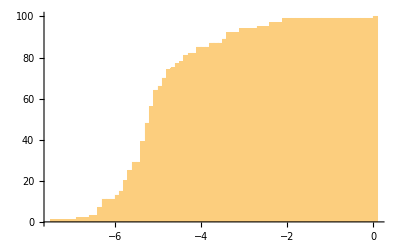

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.46119,0)(-7.46119,1)(-6.8568,2)(-6.51805,3)(-6.37591,4)(-6.37591,5)(-6.37209,6)(-6.37209,7)(-6.26182,8)(-6.2259,9)(-6.2169,10)(-6.2169,11)(-5.90214,12)(-5.90214,13)(-5.85385,14)(-5.85385,15)(-5.7973,16)(-5.7973,17)(-5.72839,18)(-5.72839,19)(-5.72475,20)(-5.639,21)(-5.639,22)(-5.61648,23)(-5.60853,24)(-5.60853,25)(-5.59093,26)(-5.59093,27)(-5.56283,28)(-5.56283,29)(-5.36219,30)(-5.36219,31)(-5.34927,32)(-5.34927,33)(-5.34915,34)(-5.34915,35)(-5.34753,36)(-5.34753,37)(-5.33365,38)(-5.33365,39)(-5.27905,40)(-5.27905,41)(-5.27315,42)(-5.27315,43)(-5.26006,44)(-5.26006,45)(-5.25515,46)(-5.25515,47)(-5.2354,48)(-5.16811,49)(-5.13929,50)(-5.13929,51)(-5.1388,52)(-5.13871,53)(-5.13871,54)(-5.10266,55)(-5.10266,56)(-5.09493,57)(-5.09493,58)(-5.08143,59)(-5.08143,60)(-5.03417,61)(-5.03417,62)(-5.02182,63)(-5.02182,64)(-4.94291,65)(-4.94291,66)(-4.86859,67)(-4.86859,68)(-4.80568,69)(-4.80568,70)(-4.76934,71)(-4.76934,72)(-4.71878,73)(-4.71878,74)(-4.6344,75)(-4.51478,76)(-4.51478,77)(-4.44122,78)(-4.38612,79)(-4.38612,80)(-4.33706,81)(-4.26999,82)(-4.04202,83)(-4.04202,84)(-4.04201,85)(-3.78536,86)(-3.78536,87)(-3.44547,88)(-3.44547,89)(-3.3351,90)(-3.3351,91)(-3.31804,92)(-3.00008,93)(-3.00008,94)(-2.69762,95)(-2.37405,96)(-2.31794,97)(-2.05943,98)(-2.01872,99)(0.,100)(0.5,100)

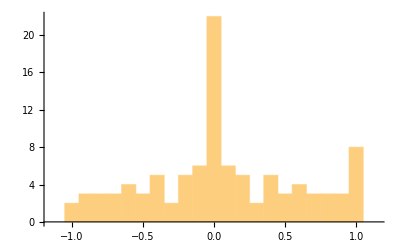

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.980146,1)(-0.962232,2)(-0.928826,3)(-0.909415,4)(-0.850695,5)(-0.835708,6)(-0.796104,7)(-0.765797,8)(-0.718489,9)(-0.704544,10)(-0.692143,11)(-0.627972,12)(-0.597123,13)(-0.589007,14)(-0.573457,15)(-0.516836,16)(-0.507115,17)(-0.483803,18)(-0.435697,19)(-0.419212,20)(-0.394375,21)(-0.390055,22)(-0.37141,23)(-0.321427,24)(-0.312967,25)(-0.238075,26)(-0.229308,27)(-0.194546,28)(-0.19272,29)(-0.182182,30)(-0.149965,31)(-0.133474,32)(-0.131599,33)(-0.100714,34)(-0.0774486,35)(-0.0554426,36)(-0.0351268,37)(-0.0296562,38)(-0.0157957,39)(0.,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.0157957,56)(0.0296562,57)(0.0351268,58)(0.0554426,59)(0.0774486,60)(0.100714,61)(0.131599,62)(0.133474,63)(0.149965,64)(0.182182,65)(0.19272,66)(0.194546,67)(0.229308,68)(0.238075,69)(0.312967,70)(0.321427,71)(0.37141,72)(0.390055,73)(0.394375,74)(0.419212,75)(0.435697,76)(0.483803,77)(0.507115,78)(0.516836,79)(0.573457,80)(0.589007,81)(0.597123,82)(0.627972,83)(0.692143,84)(0.704544,85)(0.718489,86)(0.765797,87)(0.796104,88)(0.835708,89)(0.850695,90)(0.909415,91)(0.928826,92)(0.962232,93)(0.980146,94)(1.,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

247

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersHungarian=TopicClusters;
```

```mathematica
Timing[PhuTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{221.828,Null}

```mathematica
Timing[PhuT=Table[v=Table[prepP=PhuTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[PhuT];]
```

{1.57813,Null}

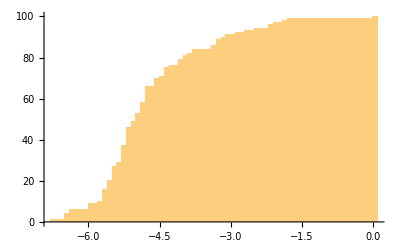

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-7.70638,0)(-6.70638,1)(-6.43412,2)(-6.43412,3)(-6.4316,4)(-6.35135,5)(-6.35135,6)(-5.97304,7)(-5.95922,8)(-5.95922,9)(-5.7619,10)(-5.6834,11)(-5.6834,12)(-5.64053,13)(-5.64053,14)(-5.60709,15)(-5.60709,16)(-5.58296,17)(-5.58296,18)(-5.5071,19)(-5.5071,20)(-5.49432,21)(-5.49432,22)(-5.48492,23)(-5.48492,24)(-5.45434,25)(-5.40062,26)(-5.40062,27)(-5.38079,28)(-5.38079,29)(-5.29839,30)(-5.29839,31)(-5.28232,32)(-5.28232,33)(-5.27285,34)(-5.27285,35)(-5.25676,36)(-5.25676,37)(-5.1868,38)(-5.1868,39)(-5.17478,40)(-5.17478,41)(-5.16356,42)(-5.16356,43)(-5.1605,44)(-5.1605,45)(-5.11768,46)(-5.09231,47)(-5.09231,48)(-5.08928,49)(-4.95029,50)(-4.95029,51)(-4.93867,52)(-4.93867,53)(-4.89519,54)(-4.89519,55)(-4.88664,56)(-4.83037,57)(-4.83037,58)(-4.78061,59)(-4.78061,60)(-4.76893,61)(-4.76893,62)(-4.73355,63)(-4.73355,64)(-4.71037,65)(-4.71037,66)(-4.59077,67)(-4.59077,68)(-4.54944,69)(-4.54944,70)(-4.48189,71)(-4.38732,72)(-4.38732,73)(-4.34033,74)(-4.34033,75)(-4.28905,76)(-4.06999,77)(-4.06999,78)(-4.04024,79)(-3.93419,80)(-3.93419,81)(-3.81895,82)(-3.73059,83)(-3.73059,84)(-3.35938,85)(-3.35938,86)(-3.26069,87)(-3.22028,88)(-3.22028,89)(-3.11051,90)(-3.01094,91)(-2.89454,92)(-2.67408,93)(-2.48301,94)(-2.17166,95)(-2.12899,96)(-2.05877,97)(-1.81343,98)(-1.7559,99)(0.,100)(0.5,100)

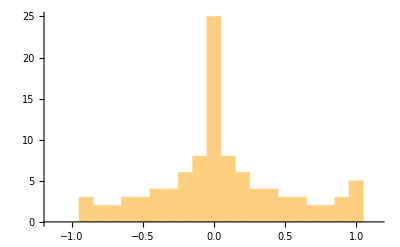

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.919749,1)(-0.905543,2)(-0.88067,3)(-0.830762,4)(-0.764743,5)(-0.742716,6)(-0.670356,7)(-0.648069,8)(-0.611456,9)(-0.578691,10)(-0.522753,11)(-0.518465,12)(-0.508945,13)(-0.441778,14)(-0.421141,15)(-0.383886,16)(-0.37431,17)(-0.342081,18)(-0.311894,19)(-0.275404,20)(-0.255648,21)(-0.246631,22)(-0.185881,23)(-0.182805,24)(-0.176147,25)(-0.175988,26)(-0.163438,27)(-0.139326,28)(-0.135726,29)(-0.11189,30)(-0.0992961,31)(-0.0856581,32)(-0.0811821,33)(-0.0515781,34)(-0.050684,35)(-0.0472101,36)(-0.0259198,37)(-0.0194337,38)(0.,39)(0.,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.,57)(0.0194337,58)(0.0259198,59)(0.0472101,60)(0.050684,61)(0.0515781,62)(0.0811821,63)(0.0856581,64)(0.0992961,65)(0.11189,66)(0.135726,67)(0.139326,68)(0.163438,69)(0.175988,70)(0.176147,71)(0.182805,72)(0.185881,73)(0.246631,74)(0.255648,75)(0.275404,76)(0.311894,77)(0.342081,78)(0.37431,79)(0.383886,80)(0.421141,81)(0.441778,82)(0.508945,83)(0.518465,84)(0.522753,85)(0.578691,86)(0.611456,87)(0.648069,88)(0.670356,89)(0.742716,90)(0.764743,91)(0.830762,92)(0.88067,93)(0.905543,94)(0.919749,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Word translation

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
HungarianRef=TopicClustersHungarian;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapHungarian=StringReplace[ImportString[#,"HTML"]&/@StringReplace[StringReplace[StringReplace[StringSplit[Import["Büszkeség és balítélet.txt"],("l"|DigitCharacter)..~~". "~~"FEJEZET"],{"Büszkeség és balítélet -"~~DigitCharacter..~~"/199":>"","\n":>"\n舜"}],{(s:("舜"~~Repeated[Except["\n"],{1,80}]))~~"\n":>s<>"垚"}],{"舜":>""}],{"垚":>"\n\n"}];
```

```mathematica
Length[PandPChapHungarian]
```

61

```mathematica
VecHungarian=Table[{HungarianRef_⟦k,1⟧,StringCount[PandPChapHungarian,WordBoundary~~Alternatives@@(#_⟦1⟧&/@HungarianRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[HungarianRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecHungarian,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100 √61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedHungarianRef=Reverse[SortBy[Table[Cases[HungarianRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

75

```mathematica
Length[SiftedHungarianRef]
```

76

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{52.5335,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for Hungarian

```mathematica
ToTopicsHungarian=SiftedHungarianRef;
```

```mathematica
Length[ToTopicsHungarian]
```

76

```mathematica
ToDeltaHungarian=ReadDelta[#]&/@ToTopicsHungarian;
```

```mathematica
ToNHungarian=(#_⟦3⟧-1)&/@ToTopicsHungarian;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersHungarian,PhuTopic,#_⟦1⟧&/@ToTopicsHungarian];]
```

{138.187,Null}

```mathematica
ToKinHungarian=KinQ;
```

```mathematica
ToEtaHungarian=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsHungarian,ToKinHungarian}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.018041,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{brighton,2},{brightoni,3},{brightonba,11},{brightonban,4},{brightonból,4}}
0.86486110100833 | 1 | 1
{{de,39}}->{{bourgh,31},{bourghhoz,1},{bourghnak,3},{bourghot,1},{bourghtól,1}}
0.87542986023652 | 1 | 1
{{Derbyshire,24}}->{{derbyshire,2},{derbyshire-be,1},{derbyshire-ben,8},{derbyshire-ből,4},{derbyshire-i,6},{derbyshire-nek,1},{derbyshire-nél,2},{derbyshire-t,1}}
0.83906647067764 | 1 | 1
{{library,23}}->{{könyvtárszoba,1},{könyvtárszobába,6},{könyvtárszobában,4},{könyvtárszobából,1},{könyvtárszobája,1},{könyvtár,1},{könyvtárat,1},{könyvtárba,3},{könyvtárban,2},{könyvtárból,1},{könyvtárában,2},{könyvtárát,1},{könyvtáram,1}}
0.93568564158507 | 1 | 1
{{London,55}}->{{london,4},{londonba,31},{londonban,37},{londonból,14},{londonhoz,1},{londoni,15},{londonig,2},{londonnak,3},{londonon,1},{londont,2}}
0.85019492437641 | 1 | 1
{{Meryton,57}}->{{meryton,1},{merytoni,12},{merytonba,17},{merytonban,19},{merytonból,3},{merytonig,2},{merytonon,1},{merytonról,1},{merytontól,3}}
0.86041350905035 | 1 | 1
{{money,26}}->{{készpénznek,2},{pénzajándékok,1},{pénzhiány,2},{pénzügyeket,1},{pénzzavarba,1},{tűpénzed,1},{zsebpénze,1},{pénz,4},{pénzben,1},{pénzen,1},{pénzért,2},{pénzre,1},{pénzről,1},{pénzt,8},{pénzzel,1},{pénze,2},{pénzébe,1},{pénzén,1},{pénzem,1},{pénzüket,1},{pénzünk,1}}
0.85523575030667 | 1 | 1
{{Mrs,343}}->{{mrs,381}}
0.91478438635997 | 1 | 1
{{Netherfield,73}}->{{netherfield,5},{netherfieldbe,17},{netherfieldben,19},{netherfieldből,8},{netherfielddel,1},{netherfieldet,5},{netherfieldre,1},{netherfieldről,1},{netherfieldi,22},{netherfieldieket,1}}
0.86138156561354 | 1 | 1
{{park,22}}->{{park,8},{parkba,4},{parkban,3},{parkból,1},{parkja,2},{parknak,1},{parkon,1},{parkot,5},{parkra,1},{parktól,1},{parkjuk,1}}
0.78477118582857 | 1 | 1
{{Pemberley,53}}->{{pemberley,7},{pemberleybe,8},{pemberleyben,16},{pemberley-ház,1},{pemberleyhez,1},{pemberleyi,15},{pemberleyre,1},{pemberleyt,5}}
0.77154364342101 | 1 | 1
{{Rosings,49}}->{{rosings,5},{rosingsba,8},{rosingsban,10},{rosingsból,1},{rosingshoz,1},{rosingsi,20},{rosingsról,2},{rosingstól,1},{rosingsiak,1}}
0.93881086448019 | 1 | 1
{{sir,78}}->{{william,44},{williamet,3},{williamhez,1},{williammel,2},{williamnek,1},{williamék,1}}
0.87854232638277 | 2 | 2
{{William,40},{William's,6}}->{{sir,53}}
0.89056814115661 | 1 | 1
{{ball,34},{balls,8}}->{{bállal,1},{bálterembe,1},{bálteremben,2},{bál,17},{bálba,2},{bálban,1},{báli,1},{bálja,1},{bálnak,1},{bálon,14},{bálra,2},{bálról,4},{bált,3},{bálok,1},{bálokat,3},{báloknak,1},{bálokra,1}}
0.86000449685893 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{catherine,117},{catherine-en,1},{catherine-hez,1},{catherine-nek,5},{catherine-nel,2},{catherine-nél,1},{catherine-ről,1},{catherine-t,14},{catherine-től,2}}
0.93307846046211 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{charlotte,73},{charlotte-,1},{charlotte-ba,1},{charlotte-ban,1},{charlotte-ét,1},{charlotte-hoz,2},{charlotte-jától,1},{charlotte-nak,7},{charlotte-om,1},{charlotte-omban,1},{charlotte-omtól,1},{charlotte-ot,4},{charlotte-tal,5},{charlotte-tól,2}}
0.85026752692035 | 1 | 1
{{civilities,7},{civility,42}}->{{udvarias,17},{udvariasan,19},{udvariaskodás,2},{udvariaskodása,2},{udvariaskodását,2},{udvariaskodást,1},{udvariasság,3},{udvariassága,5},{udvariasságáért,1},{udvariasságán,1},{udvariasságát,1},{udvariasságával,1},{udvariasságban,1},{udvariassággal,18},{udvariasságnak,1},{udvariasságnál,1},{udvariasságot,2},{udvariasságra,2},{legudvariasabban,1},{udvariasabb,1},{udvariasabban,1}}
0.74982022558015 | 1 | 1
{{Collins,156},{Collins's,24}}->{{collins,162},{collinsból,1},{collinshoz,3},{collinsnak,13},{collinsról,5},{collinst,8},{collinstól,4},{collinsék,7},{collinsékat,1},{collinséknak,1},{collinsékra,1}}
0.87361692090617 | 1 | 1
{{colonel,65},{colonel's,1}}->{{ezredes,45},{ezredeshez,4},{ezredesné,1},{ezredesnek,6},{ezredesnét,1},{ezredest,6},{ezredestől,3},{ezredesének,1},{ezredesékkel,1},{ezredeséknél,1}}
0.81936868163722 | 1 | 1
{{dinner,33},{dinners,2}}->{{vacsora,14},{vacsorához,4},{vacsoránál,1},{vacsorára,16},{vacsoráról,1},{vacsorát,4},{vacsorától,1},{vacsorával,1},{vacsoránk,1}}
0.75814983939672 | 1 | 1
{{father,116},{father's,19}}->{{apa,3},{apád,2},{apai,2},{édesapád,3},{édesapáddal,1},{édesapádhoz,1},{apja,39},{apjához,2},{apjának,5},{apjára,3},{apjáról,1},{apját,7},{apjától,2},{apjával,4},{édesapja,12},{édesapjához,1},{édesapjaként,1},{édesapjának,1},{apám,14},{apámat,1},{apámnak,3},{édesapám,12},{édesapámmal,1},{édesapánk,2},{édesapánkat,1},{apátok,2},{apátokkal,1},{apjuk,13},{apjukat,1},{apjukkal,1},{apjuknak,5},{apjukra,1},{apjukról,1},{édesapjuk,1},{édesapjuktól,1}}
0.88976699771411 | 1 | 1
{{Fitzwilliam,32},{Fitzwilliam's,5}}->{{fitzwilliam,44}}
0.73867227002823 | 1 | 1
{{four,33},{four-and-twenty,1}}->{{tizenegyre,1},{városnegyedben,1},{negyven,1},{négy,16},{négyen,1},{négyet,1},{négy-ötezer,2},{négyéves,2},{negyedben,1},{negyedik,4},{négyszemközt,6},{négyünknek,1}}
0.79939844270838 | 1 | 1
{{Jane,263},{Jane's,28}}->{{jane,289},{jane-,1},{jane-be,1},{jane-em,1},{jane-ért,2},{jane-hez,6},{jane-nek,15},{jane-nel,10},{jane-nél,1},{jane-re,9},{jane-ről,2},{jane-t,25},{jane-től,2}}
0.8819208935737 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{kitty,60},{kittyt,6}}
0.90426190806422 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{lizzy,73},{lizzynek,3},{lizzyről,1},{lizzyt,7},{lizzyvel,1},{lizzym,17}}
0.92624510896287 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{lydia,171},{lydiában,1},{lydiáért,3},{lydiához,1},{lydián,1},{lydiának,13},{lydiára,4},{lydiáról,1},{lydiát,23},{lydiától,2},{lydiával,3},{lydiáé,1},{lydiáék,2},{lydiám,4},{lydiámnak,1},{lydiámra,1},{lydiánk,1}}
0.88225649538486 | 1 | 1
{{Mary,38},{Mary's,1}}->{{mary,30},{maryért,1},{marynek,3},{maryt,4},{marytonban,1}}
0.84581570900015 | 1 | 1
{{poor,38},{poorly,3}}->{{megszegését,1},{megszegett,1},{szegény,34},{szegényebb,1},{szegények,1},{szegényekkel,1},{szegénységbe,1},{szegték,1},{beszegem,1}}
0.75186466263604 | 1 | 1
{{surprise,37},{surprised,35}}->{{leleplezni,2},{meglep,2},{meglepetés,8},{meglepetése,1},{meglepetésében,2},{meglepetéséből,1},{meglepetésemre,1},{meglepetésére,5},{meglepetését,2},{meglepetést,4},{meglepetéstől,2},{meglepett,7},{meglepő,5},{meglepte,9},{megleptelek,1},{meglepve,5},{meglepetve,4},{belepillantott,1}}
0.80724230804971 | 1 | 1
{{table,28},{tables,3}}->{{asztal,5},{asztalhoz,6},{asztalnál,5},{asztalon,1},{asztalra,1},{asztalról,1},{asztalt,1},{asztalokat,1},{asztaluknál,1}}
0.82465635759148 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{wickham,193},{wickhambe,1},{wickhamben,1},{wickhamen,3},{wickhamet,25},{wickhamhez,1},{wickhammel,19},{wickhamnek,15},{wickhamnél,1},{wickhamre,8},{wickhamről,9},{wickhamtől,4},{wickham-ügyben,1},{wickhamé,1},{wickhamék,3},{wickhamem,1},{wickhamemet,1},{wickhamemre,1}}
0.79138838406839 | 1 | 1
{{window,16},{windows,6}}->{{ablak,2},{ablakból,4},{ablakhoz,7},{ablaknál,1},{ablakot,1},{ablaktól,1},{ablakából,3},{ablakát,1},{ablakai,1},{ablakok,1},{ablakokat,1}}
0.77098517604581 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{bennet,339},{bennetben,1},{benneték,5},{bennetékkel,1},{bennetékről,1},{benneten,1},{bennetet,23},{bennethez,3},{bennetnek,19},{bennetre,2},{bennetről,1},{bennettel,7},{bennettől,2}}
0.88718827072537 | 1 | 1
{{child,14},{children,25},{childhood,1}}->{{gyerekből,1},{gyereket,1},{gyermek,2},{gyermeket,1},{gyermeki,1},{gyermeknek,1},{gyermekét,1},{gyerekei,1},{gyermekei,3},{gyermekeinek,1},{gyermekeit,3},{gyermekeivel,2},{gyerekeim,1},{gyermekeim,1},{gyerekek,2},{gyerekekkel,1},{gyermekek,1},{gyermekeket,1},{gyermekekkel,1},{gyermekeknek,1},{gyermekekre,1},{gyermekem,3},{gyermekük,1},{gyermekükkel,1}}
0.91755147410469 | 1 | 1
{{cried,91},{cry,1},{crying,2}}->{{közbekiáltani,1},{kiáltotta,39},{kiáltották,1},{felkiáltás,1},{felkiáltásait,1},{felkiáltásával,1},{felkiáltások,2},{felkiáltott,7},{kiáltott,45},{kialakul,1},{kialakult,2},{kiállotta,1}}
0.85265381637352 | 1 | 1
{{evening,72},{evening's,2},{evenings,4}}->{{est,10},{esti,6},{este,63},{estén,1},{estére,3},{estéről,1},{estét,11},{estéjén,1},{esténk,1}}
0.83679335369867 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{gardiner,77},{gardinerben,1},{gardinernek,2},{gardinerrel,2},{gardinert,8},{gardinertől,2},{gardinerék,13},{gardineréket,2},{gardinerékhez,1},{gardineréktől,2}}
0.76714284972146 | 1 | 1
{{hand,24},{handed,3},{hands,7}}->{{kezeskedem,1},{kezeskedni,1},{kezet,6},{kéz,1},{keze,4},{kezébe,2},{kezében,6},{kezéből,1},{kezére,2},{kezét,20},{kezével,1},{kezedet,1},{kezelhetők,1},{kezelte,1},{kezem,1},{kezemet,3},{kezemre,1},{kezüket,1},{kezünkből,1},{kezünkre,1}}
0.81144735291871 | 1 | 1
{{husband,42},{husband's,8},{husbands,4}}->{{férj,1},{férje,26},{férjébe,1},{férjében,1},{férjéhez,1},{férjének,5},{férjes,3},{férjet,6},{férjét,8},{férjével,3},{férjhez,37},{férjjel,2},{férjnél,1},{férjed,1},{férjedet,3},{férjednek,1},{férjem,1}}
0.85695390579261 | 1 | 1
{{letter,115},{letters,16},{letter-paper,1}}->{{levélpapír,2},{levélírásra,1},{levélírást,1},{levélíró,1},{levél,42},{levélbe,1},{levélben,12},{levélből,3},{levélen,1},{levelet,69},{levéllel,2},{levélnek,2},{levélre,4},{levele,12},{levelében,6},{leveléből,3},{levelének,1},{levelére,6},{levelét,13},{leveledből,1},{leveledet,1},{levelednek,1},{leveleit,1},{leveleik,1},{leveleket,4},{levelekre,1},{levelemet,4},{levelez,1},{levelezés,1},{levelezésből,1},{levelezéssel,1},{levelezést,1},{levelezésük,1},{levelezett,1}}
0.81139564065881 | 1 | 1
{{man,145},{man's,5},{men,33}}->{{embere,1},{ember,115},{emberben,3},{ember-e,1},{emberen,1},{emberhez,2},{emberi,7},{emberiesség,1},{emberiségben,1},{embernek,11},{emberre,2},{emberré,2},{emberrel,5},{emberről,6},{embert,21},{emberére,1},{emberét,1},{emberek,20},{emberekben,1},{embereken,1},{embereket,9},{emberekhez,1},{emberekkel,4},{embereknek,1},{emberismeretében,1},{emberismeretéből,1}}
0.87117680766759 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{annyiféle,1},{mamának,2},{anya,3},{anyához,1},{anyáról,1},{anyát,1},{anyával,1},{anyja,41},{anyjához,1},{anyjának,10},{anyjára,1},{anyját,4},{anyjától,1},{anyjával,3},{édesanyja,13},{édesanyjának,5},{mama,27},{anyai,2},{anyjuk,11},{anyjukat,3},{anyjukhoz,1},{anyjuknak,2},{édesanyjuk,1},{édesanyjukat,1},{édesanyjuknak,2},{anyád,2},{anyádnak,1},{édesanyádat,1},{anyám,3},{anyámhoz,1},{anyámnak,1},{anyámnál,1},{anyánk,1},{anyánkat,1}}
0.94637519101271 | 1 | 1
{{nephew,20},{nephew's,2},{nephews,2}}->{{unokaöcs,1},{unokaöccse,14},{unokaöccséből,1},{unokaöccséhez,3},{unokaöccsének,2},{unokaöccsét,2},{unokaöccsétől,1},{unokaöccsével,3},{unokaöccsei,1},{unokaöcséhez,1},{unokaöcsém,6},{unokaöcsémet,2},{unokaöcsémhez,1}}
0.888523902642 | 1 | 1
{{niece,20},{niece's,2},{nieces,9}}->{{unokahúga,14},{unokahúgához,2},{unokahúgának,2},{unokahúgára,3},{unokahúgát,2},{unokahúgával,1},{unokahúgai,6},{unokahúgainak,2},{unokahúgait,5},{unokahúgaimat,1},{unokahúgaimnak,1},{unokanővérét,1},{unokahúgom,7},{unokahúgomat,2},{unokahúgomról,1},{unokahúguk,2},{unokahúgukat,1},{unokahúgukkal,1},{unokanővérük,1}}
0.78550223944699 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{philips,27},{philipsben,1},{philipset,2},{philipsnek,3},{philipsék,1},{philipsékhez,1},{philipsékkel,1},{philipséknél,1}}
0.8487839305702 | 1 | 1
{{read,40},{reading,14},{reader,3}}->{{leolvasta,1},{olvas,3},{olvasás,5},{olvasásába,1},{olvasásba,3},{olvasáshoz,2},{olvasásnak,1},{olvasásnál,2},{olvasásra,2},{olvasással,2},{olvasást,2},{olvasd,1},{olvashatott,1},{olvashatta,1},{olvasmányaim,1},{olvasna,1},{olvasni,3},{olvasott,9},{olvasta,7},{olvastad,1},{olvastam,1},{olvasok,1},{olvasom,2}}
0.78489933839318 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{bácsi,10},{bácsin,1},{bácsit,2},{bácsitól,1},{bácsival,1},{nagybácsi,3},{nagybátyja,18},{nagybátyjához,2},{nagybátyjának,3},{nagybátyját,2},{nagybátyád,6},{nagybátyádat,2},{nagybátyáddal,2},{nagybátyádnak,2},{nagybátyjai,2},{nagybátyjuk,5},{bácsim,1},{nagybácsim,1},{nagybácsimat,1},{nagybácsink,2},{nagybátyám,3},{nagybátyámat,2},{nagybátyámhoz,1},{nagybátyánk,1},{nagybátyátok,1}}
0.86629563739804 | 1 | 1
{{year,28},{years,33},{years',2}}->{{év,10},{évben,4},{éven,1},{éves,15},{évet,3},{évi,12},{évig,3},{évnél,1},{évvel,13},{éve,5},{éveiben,1},{évek,1},{éveken,1},{évekig,3},{évszak,2},{évszakhoz,1},{évszaknak,1},{évente,2}}
0.88480293449456 | 1 | 1
{{brother,62},{brotherly,2},{brother's,13},{brothers,2}}->{{bátyja,17},{bátyjához,2},{bátyjának,1},{bátyját,2},{bátyjával,1},{fivér,1},{fivéren,1},{bátyám,5},{bátyáméknál,1},{fivére,5},{fivérével,2},{öccse,10},{öccséhez,1},{öccsének,1},{öccsénél,1},{öccsét,1},{fivérem,3},{fivérük,7},{fivérükkel,1},{öccsük,7},{fivérüké,1}}
0.84789918358961 | 1 | 1
{{came,90},{come,93},{comes,16},{coming,61}}->{{gyere,7},{bejön,1},{jöhet,3},{jöhetnek,1},{jön,29},{jön-e,1},{jönni,5},{jönnie,1},{jöttél,2},{jöttem,7},{kijöttem,1},{lejön,1},{megjöttem,1},{jöjj,2},{jöjjenek,2},{jöjjön,10},{jöjjetek,1},{jöjjünk,1},{jönne,1},{jönnek,1},{jönnének,1},{kijönnek,1},{bejött,3},{jött,63},{lejött,3},{megjött,6},{bejöttek,4},{jöttek,8},{megjöttek,1},{jöttetek,1},{jövendő,9},{jövet,1},{jövő,12},{jövedelem,1},{jövedelemmel,1},{jövedelme,6},{jövedelmemből,1},{jövedelmet,1},{jövedelmét,1},{jövedelmetek,1},{jövedelmez,1},{jövedelmező,2},{jövedelmük,3},{jövedelmüknél,1},{jövedelmükön,1},{jövevényeket,1},{jövőben,8},{jövőjéről,1},{jövőre,2},{jövőtől,1},{jövök,2}}
0.88794709072984 | 1 | 1
{{character,64},{characters,3},{characterise,1},{characteristic,2}}->{{jellemű,1},{jellem,5},{jellembe,1},{jellemes,1},{jellemnek,1},{jellemvonásaikat,1},{jellemvonásait,1},{jellemvonást,1},{jelleme,9},{jellemében,4},{jelleméből,1},{jellemének,2},{jellemére,4},{jelleméről,6},{jellemét,16},{jellemek,1},{jelöltem,1},{jelentenél,1},{jelenteni,1},{jelentőséget,1},{jelentőségét,2},{jelentőségű,1},{kijelenteni,1},{kijelenti,1},{jelenetet,3},{jelenetre,1},{jelenettől,1},{jelenetek,1},{jelenléte,4},{jelenlétében,4}}
0.86200930357729 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{életkedvvel,1},{reménykedve,1},{jókedv,3},{jókedvben,1},{jókedvvel,2},{jókedve,1},{jókedvében,4},{jókedvén,1},{jókedvének,1},{jókedvét,2},{jókedvével,1},{jókedvük,1},{jókedvű,4},{jókedvűen,3},{jókedvűek,1},{kedvelem,1},{kedves,76},{kedvesebb,2},{kedvesebbek,1},{kedvesek,1},{kedvesem,3},{kedvesen,3},{kedveskedve,1},{kedvesnek,1},{kedvessé,1},{kedvesség,3},{kedvessége,2},{kedvességére,1},{kedvességét,1},{kedvességgel,1},{kedvességtől,1},{kedvességükből,1},{kedvességüket,1},{kedvet,2},{kedvtelése,1},{kedvteléseiből,1},{kedvvel,2},{legkedvesebb,3},{kedve,14},{kedvében,5},{kedvére,2},{kedvét,2},{kedved,1},{kedvedért,1},{kedvedet,1},{kedveli,3},{kedvelt,2},{kedvelte,4},{kedvelték,2},{megkedvelni,2},{megkedvelik,1},{kedvem,1},{kedvemben,1},{kedvemért,2},{kedvemet,1},{kedvetekért,1},{kedvük,3},{kedvükért,1},{kedveljük,1}}
0.91599055975768 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{lucasszal,3},{lucas,54},{lucashoz,1},{lucas-lakba,1},{lucas-lakban,5},{lucas-laknak,1},{lucasnak,6},{lucast,8},{lucasék,2},{lucasékat,1},{lucaséknak,1},{lucaséknál,3}}
0.84735499075544 | 1 | 1
{{vanish,1},{vanished,2},{vanity,18},{vain,20}}->{{hiú,6},{hiúság,8},{hiúsága,3},{hiúságának,2},{hiúságát,2},{hiúságomhoz,1},{hiúságomnak,1},{hiába,41}}
0.77468585683838 | 1 | 1
{{disappoint,2},{disappointed,12},{disappointing,3},{disappointment,17},{disappointments,1}}->{{csalt,1},{csalta,2},{csalták,1},{csalódás,6},{csalódása,1},{csalódásáért,1},{csalódását,1},{csalódásért,1},{csalódások,1},{csalódásra,2},{csalódást,4},{csalódhatott,1},{csalódni,1},{csalódott,7},{csalódtál,1},{csalódtam,1},{csalódva,1},{csalódottság,1},{csalódom,1},{csaltak,1},{csalódtunk,1},{csalódotton,1}}
0.84018779494584 | 1 | 1
{{happily,5},{happiness,72},{happy,83},{happier,3},{happiest,10}}->{{boldog,55},{boldogan,4},{boldoggá,7},{boldognak,4},{boldogság,17},{boldogsága,4},{boldogságához,1},{boldogságának,1},{boldogságáról,6},{boldogságát,13},{boldogságával,1},{boldogságban,1},{boldogsággal,1},{boldogsághoz,1},{boldogságnak,2},{boldogságod,1},{boldogságom,2},{boldogságomat,3},{boldogságomhoz,1},{boldogságomra,1},{boldogságot,21},{boldogságra,7},{boldogságról,2},{boldogságtól,1},{boldogságukat,3},{boldogságukban,1},{boldogságunk,1},{boldogabb,3},{legboldogabb,7},{boldogok,6}}
0.90987637838994 | 1 | 1
{{house,106},{houses,4},{household,1},{housemaid,2},{housemaids,1}}->{{hazajövetele,1},{hazautazunk,1},{idehaza,1},{hazaérkezése,2},{hazaérkezésük,1},{hazaérkeztem,1},{haza,19},{hazajön,1},{hazajönni,1},{hazamenni,2},{hazamentem,1},{házam,1},{házamba,1},{ház,31},{házad,1},{házat,14},{házba,14},{házban,11},{házból,5},{házhoz,2},{házi,1},{háznál,1},{házon,1},{házról,3},{háztól,2},{háza,4},{házába,5},{házában,4},{házából,1},{házáról,1},{házát,2},{házuk,1},{házukba,1},{házunkból,1}}
0.80567013019519 | 1 | 1
{{length,32},{long,114},{longed,9},{longing,2},{longer,44}}->{{jóakarat,2},{jóakarója,2},{akar,30},{akarás,1},{akarhat,1},{akarhatnak,1},{akarja,26},{akarják,2},{akarlak,2},{akarna,1},{akarná,4},{akarnak,3},{akarnák,1},{akarnék,3},{akarnia,1},{akarsz,5},{akart,46},{akarta,46},{akartad,1},{akarták,8},{akartam,6},{akarva,2},{akarata,4},{akaratát,3},{akaratától,1},{akaratú,1},{akarjuk,1},{akármelyiküket,1},{akartak,2},{akarod,6},{akarok,16},{akarom,16},{akartok,2},{akarunk,2}}
0.84121517969743 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{miss,303}}
0.8370866749415 | 1 | 1
{{woman,55},{womanly,1},{woman's,4},{women,19},{women's,1}}->{{növésű,1},{növekvő,2},{növelje,2},{növelné,1},{növelte,2},{nő,27},{nőnek,4},{nőnél,1},{nőre,1},{nőt,9},{nőül,3},{felnőtt,1},{nőtt,4},{nőttön-nőtt,1},{nőtagja,1}}
0.76149653713943 | 1 | 1
{{feel,39},{feeling,38},{feelingly,1},{feelings,86},{feels,4},{felt,100}}->{{érzékeny,2},{érzékenyebben,1},{érzékenységgel,1},{érzelmei,3},{érzelmeiben,2},{érzelmeikre,1},{érzelmeim,2},{érzelmeimet,1},{érzelmein,1},{érzelmeire,1},{érzelmeiről,1},{érzelmeit,15},{érzelmeivel,1},{érzelmek,3},{érzelmekért,1},{érzelmeket,5},{érzelmet,2},{érzelmi,1},{érzés,15},{érzésben,2},{érzése,4},{érzésébe,1},{érzései,6},{érzéseiben,1},{érzéseid,1},{érzéseidet,1},{érzéseik,2},{érzéseim,2},{érzéseimet,4},{érzésein,3},{érzéseinek,3},{érzéseire,1},{érzéseiről,2},{érzéseit,16},{érzéseivel,3},{érzések,5},{érzéseket,6},{érzésekkel,6},{érzéseknek,1},{érzésekre,1},{érzésekről,2},{érzésektől,1},{érzésem,3},{érzését,2},{érzéshez,1},{érzésnek,1},{érzéssé,2},{érzéssel,6},{érzést,3},{érzéstől,3},{érzésük,1},{érzett,23},{érzi,8},{érzi-e,2},{érző,1},{érzed,1},{érzek,2},{érzem,14},{érzik,2},{érzünk,1},{érzéke,3},{érzékeltetni,1},{érzékük,1}}
0.80525511288959 | 1 | 1
{{suffer,13},{suffered,8},{suffering,2},{sufferings,2},{suffers,1},{sufferer,1}}->{{szentelte,1},{szenteltek,1},{szenved,3},{szenvedés,1},{szenvedésekbe,1},{szenvedésére,1},{szenvedést,3},{szenvedett,3},{szenvedhet,1},{szenvedhetett,1},{szenvedjen,1},{szenvednek,1},{szenvedni,1},{szenvednie,3},{szenvedte,1},{szenvedek,2}}
0.81270866338488 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{levélírásra,1},{levélírást,1},{levélíró,1},{ír,14},{írás,2},{írásodra,1},{írással,1},{írást,1},{íratott,1},{írhat,3},{írhatott,1},{írhatta,1},{írnak,1},{írni,16},{írnia,1},{írt,30},{írtam,9},{leírás,1},{leírásának,1},{leírását,1},{leírásával,1},{leírásnak,1},{leírást,2},{leírjanak,1},{leírna,1},{leírni,3},{leírt,1},{leírta,1},{leírtad,1},{leírtam,1},{írj,2},{írjanak,1},{írjon,5},{írja,4},{írjál,1},{írjam,1},{írnom,2},{írok,7},{írom,2},{írta,13},{írva,1}}
0.86876405268052 | 1 | 1
{{mean,34},{meaning,14},{meanly,3},{meanness,1},{means,57},{meant,28},{meanest,1}}->{{feltehetőleg,3},{feltenni,3},{megtehet,1},{megtehetem,1},{megtehette,1},{megtenni,1},{megtennie,1},{megtettem,3},{tehetem,2},{tehetetlen,1},{tehetett,3},{teheti,10},{tehetnek,1},{tehetnék,1},{tehető,1},{tehetség,1},{tehetsége,1},{tehetséged,1},{tehetségekkel,1},{tehetségem,1},{tehetségemre,1},{tehetségénél,1},{tehetséges,2},{tehetséget,1},{tehetségét,1},{tehetségük,1},{tehette,2},{tehettek,1},{temetésére,1},{megtenné,1},{megtesz,3},{megteszi,2},{megteszek,1},{felteszem,1},{megteszem,1},{megteszünk,1},{feltette,1},{kitette,1},{letette,1},{megtett,1},{megtette,4},{megtették,2},{tettét,1},{tett-vett,1},{tétre,1},{tétova,1},{megtetted,1},{tetteiről,1},{tetteikért,1},{tetteiket,1},{tetteimről,1},{megtettek,1},{megtettünk,2},{feltevés,4},{feltevések,3},{feltevésekből,1},{feltevésekkel,1},{feltevésemben,1},{feltevésre,1},{feltevést,1},{tevékeny,2},{téves,2},{betéve,1},{feltéve,4},{kitéve,1},{megtévesztés,1},{megtévesztőbb,1},{téve,2},{tévesztett,1},{téveszthette,1}}
0.76655204850333 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedHungarianRef=Reverse[SortBy[Table[Cases[HungarianRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedHungarianRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedHungarianRef,{#_⟦1,1,2⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["PnP_EnglishHungarian.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedHungarianRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_for_Hungarian_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]]
```

EnglishLabels_for_Hungarian_PnP.txt

#### Hungarian labels

```mathematica
FromClusters=ResiftedHungarianRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
HungarianSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@StringReplace[AlphabeticSort[StringReplace[Keys[assoc],{"á":>"𝕒","é":>"𝕖","í":>"𝕚","ó":>"𝕠","ő":>"𝕆","ú":>"𝕦","ű":>"𝕌"}],"Hungarian"],{"𝕒":>"á","𝕖":>"é","𝕚":>"í","𝕠":>"ó","𝕆":>"ő","𝕦":>"ú","𝕌":>"ű"}])]
```

```mathematica
HungarianCompress[w_]:=(Lprot=Max[0,Max[Flatten[StringLength/@StringCases[w," "..]]]];StringTake[#,UpTo[Lprot]]<>StringReplace[StringDrop[#,UpTo[Lprot]],{}]&/@w)
```

```mathematica
HungarianDecompress[w_]:=StringReplace[w,{}]
```

```mathematica
ClusterCount={{"dætter","dætters","døtre","guddætter"},{10,72,83,100}}
```

{{dætter,dætters,døtre,guddætter},{10,72,83,100}}

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[cl];prep=HungarianCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{dætter   ,10},{dætters  ,72},{døtre    ,83},{guddætter,100}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,HungarianDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
d
10 | 2
æ
10 | 3
t
10 | 4
t
10 | 5
e
10 | 6
r
10 | 7
 
10 | 8
 
10 | 9
 
10
1
d
72 | 2
æ
72 | 3
t
72 | 4
t
72 | 5
e
72 | 6
r
72 | 7
s
72 | 8
 
72 | 9
 
72
1
d
83 | 2
ø
83 | 3
t
83 | 4
r
83 | 5
e
83 | 6
 
83 | 7
 
83 | 8
 
83 | 9
 
83
1
g
100 | 2
u
100 | 3
d
100 | 4
d
100 | 5
æ
100 | 6
t
100 | 7
t
100 | 8
e
100 | 9
r
100

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{9, ,10},{9, ,72},{9, ,83},{9,r,100}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
d
10 | 1
d
72 | 1
d
83 | 1
g
100
2
æ
10 | 2
æ
72 | 2
ø
83 | 2
u
100
3
t
10 | 3
t
72 | 3
t
83 | 3
d
100
4
t
10 | 4
t
72 | 4
r
83 | 4
d
100
5
e
10 | 5
e
72 | 5
e
83 | 5
æ
100
6
r
10 | 6
r
72 | 6
 
83 | 6
t
100
7
 
10 | 7
s
72 | 7
 
83 | 7
t
100
8
 
10 | 8
 
72 | 8
 
83 | 8
e
100
9
 
10 | 9
 
72 | 9
 
83 | 9
r
100

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
g
100 | 1
d
165 |  | 
2
u
100 | 2
ø
83 | 2
æ
82 | 
3
d
100 | 3
t
165 |  | 
4
d
100 | 4
r
83 | 4
t
82 | 
5
æ
100 | 5
e
165 |  | 
6
t
100 | 6
 
83 | 6
r
82 | 
7
t
100 | 7
 
83 | 7
s
72 | 7
 
10
8
e
100 | 8
 
165 |  | 
9
r
100 | 9
 
165 |  |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{6},t,100,0},{{6}, ,83,100},{{6},r,82,183}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["HungarianLabels_PnP.txt",StringReplace[StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=StringReplace[ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,"ß":>"𝕊"]],"𝕊":>"ß"];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.4],10^-3]]])<>"}{"<>temp<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]],{"Ő":>"\\H{O}","Ű":>"\\H{U}"}]];
```

```mathematica
Export["EnglishHungarian_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```